# Dodecahedral Graph

### Author

Eric W. Weisstein
March 29, 2021

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GraphTheory/DodecahedralGraph.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/DodecahedralGraph.html.

©2021 Wolfram Research, Inc. except for portions noted otherwise

## Embeddings

### All

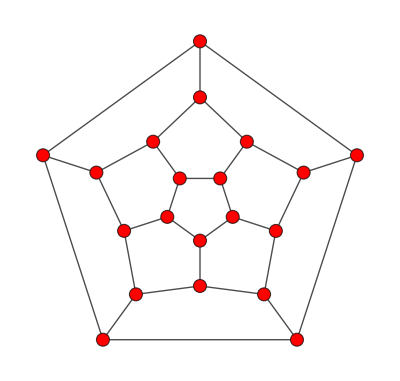
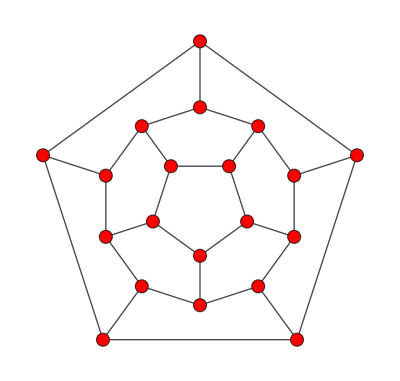
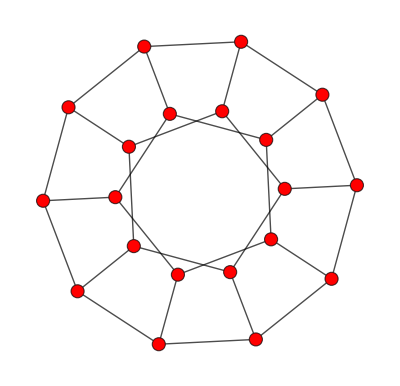
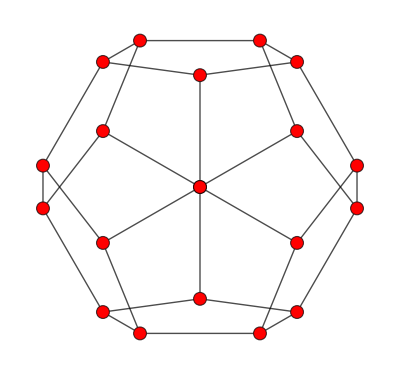
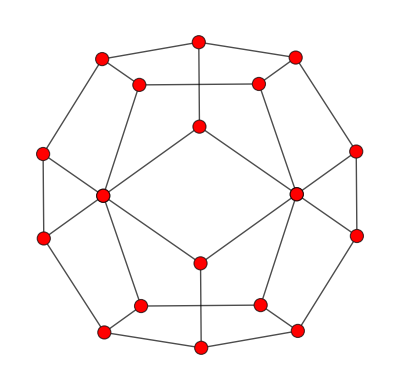
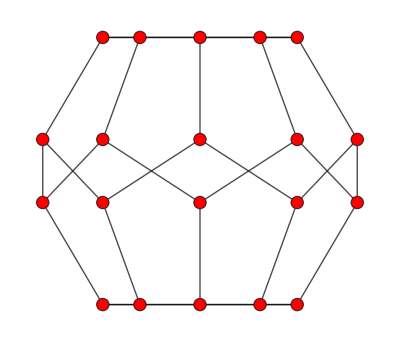
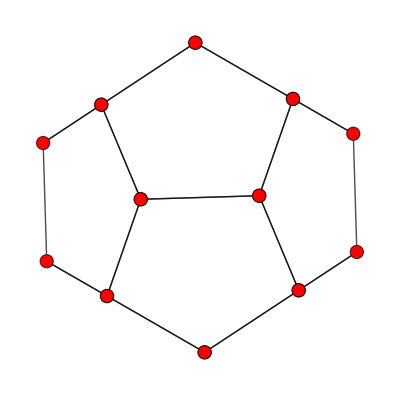
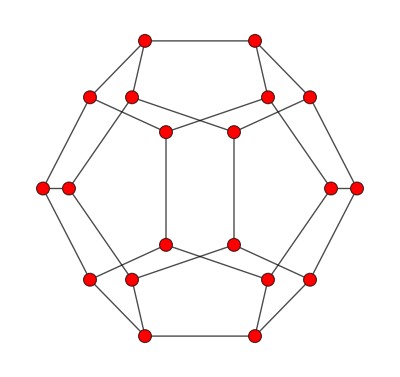

```mathematica
GraphData["DodecahedralGraph","Graph","All"]//StyleGraphs
```

### GeneralizedPetersen

```mathematica
GraphData["DodecahedralGraph","Graph","GeneralizedPetersen"]//StyleGraphs
```

{-Graphics-}

### IntegerCoordinates

```mathematica
GraphData["DodecahedralGraph","Graph","IntegerCoordinates"]//StyleGraphs
```

{-Graphics-}

### Integral

```mathematica
GraphData["DodecahedralGraph","Graph","Integral"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-}

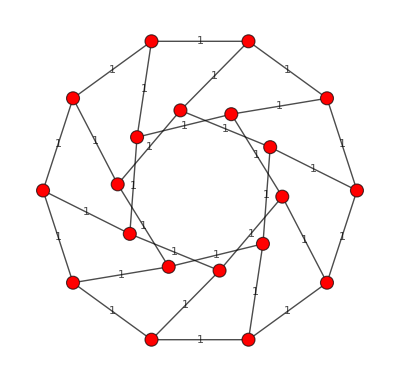
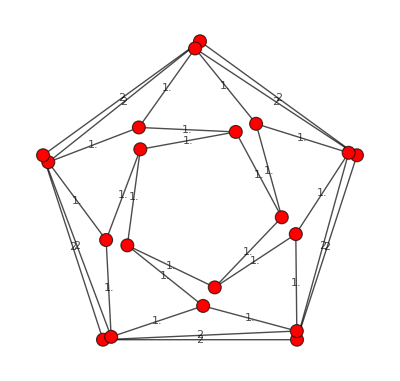
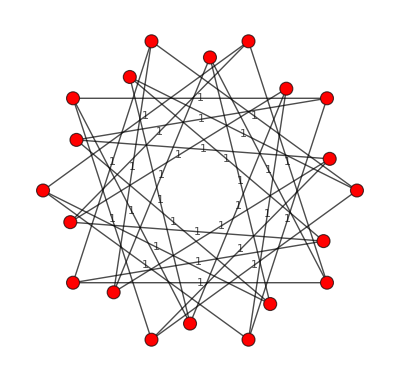

```mathematica
IntegralDrawing/@GraphData["DodecahedralGraph","Graph","Integral"]//StyleGraphs
```

### LCF

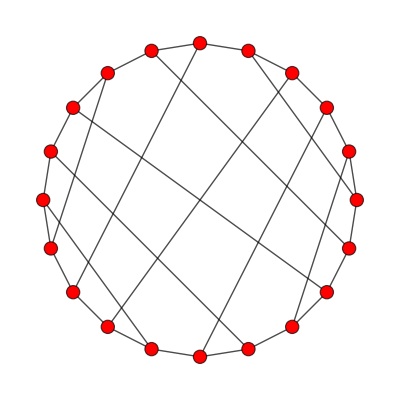

```mathematica
GraphData["DodecahedralGraph","Graph","LCF"]//StyleGraphs
```

### MinimalCrossing

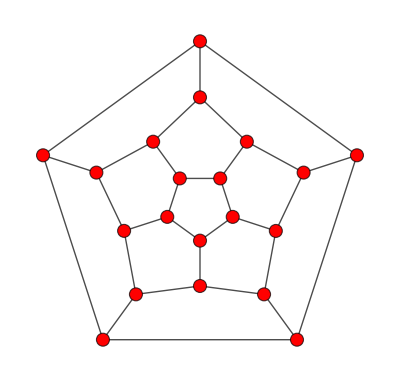
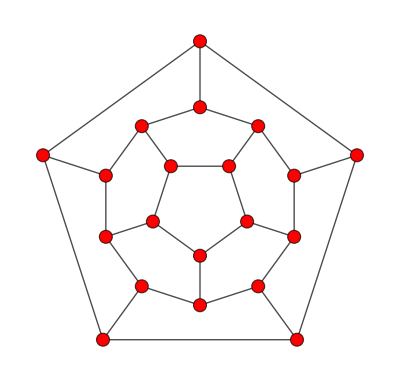
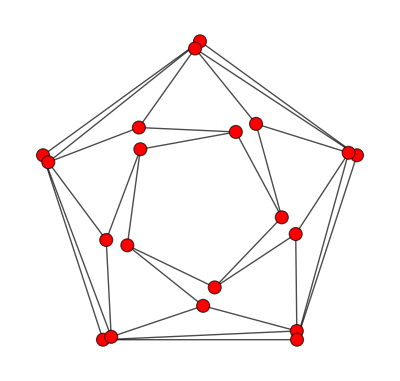

```mathematica
GraphData["DodecahedralGraph","Graph","MinimalCrossing"]//StyleGraphs
```

### MinimalIntegral

```mathematica
GraphData["DodecahedralGraph","Graph","MinimalIntegral"]//StyleGraphs
```

{-Graphics-,-Graphics-}

```mathematica
IntegralDrawing/@GraphData["DodecahedralGraph","Graph","MinimalIntegral"]//StyleGraphs
```

{-Graphics-,-Graphics-}

### MinimalPlanarIntegral

```mathematica
IntegralDrawing/@GraphData["DodecahedralGraph","Graph","MinimalPlanarIntegral"]//StyleGraphs
```

{-Graphics-}

### Planar

```mathematica
GraphData["DodecahedralGraph","Graph","Planar"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-}

### Perspective

```mathematica
GraphData["DodecahedralGraph","Graph","Perspective"]//StyleGraphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### UnitDistance

```mathematica
GraphData["DodecahedralGraph","Graph","UnitDistance"]//StyleGraphs
```

{-Graphics-,-Graphics-}

### 3-D

```mathematica
GraphData["DodecahedralGraph","Graph",{"3D","All"}]//StyleGraphs
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

### 3-D Polyhedron

```mathematica
GraphData["DodecahedralGraph","Graph",{"3D","Polyhedron"}]//StyleGraphs
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Embeddings

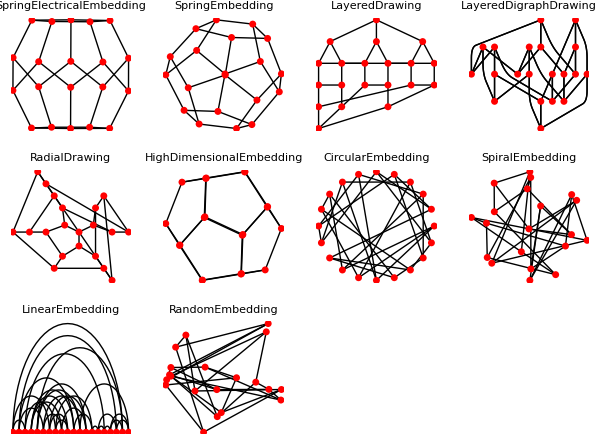

```mathematica
GraphDataEmbeddings["DodecahedralGraph"]
```

## Projections

```mathematica
Manipulate[PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{a,b,c}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

### {1, 0, 0}

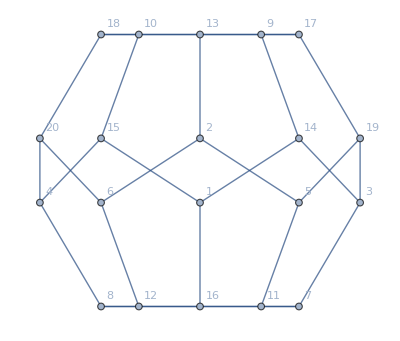

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{1,0,.0001,π/2},VertexLabels->"Name"]
```

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{1,0,z,π/2},VertexLabels->"Name"]
```

```mathematica
v=Lookup[Options[%],VertexCoordinates];
```

```mathematica
Limit[v,z->0,Direction->"FromBelow"]//FullSimplify
```

{{0,Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668},{0,Root-0.263Root[1-20 #1^2+80 #1^4&,2]-0.2628655560595668},{1/4 (-3-√5),Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668},{1/4 (3+√5),Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668},{1/4 (-1-√5),Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668},{1/4 (1+√5),Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668},{1/4 (-1-√5),√(5/8+11/(8 √5))},{1/4 (1+√5),√(5/8+11/(8 √5))},{-1/2,Root-1.11Root[1-100 #1^2+80 #1^4&,1]-1.1135163644116068},{1/2,Root-1.11Root[1-100 #1^2+80 #1^4&,1]-1.1135163644116068},{-1/2,√(5/8+11/(8 √5))},{1/2,√(5/8+11/(8 √5))},{0,Root-1.11Root[1-100 #1^2+80 #1^4&,1]-1.1135163644116068},{1/4 (-1-√5),Root-0.263Root[1-20 #1^2+80 #1^4&,2]-0.2628655560595668},{1/4 (1+√5),Root-0.263Root[1-20 #1^2+80 #1^4&,2]-0.2628655560595668},{0,√(5/8+11/(8 √5))},{1/4 (-1-√5),Root-1.11Root[1-100 #1^2+80 #1^4&,1]-1.1135163644116068},{1/4 (1+√5),Root-1.11Root[1-100 #1^2+80 #1^4&,1]-1.1135163644116068},{1/4 (-3-√5),Root-0.263Root[1-20 #1^2+80 #1^4&,2]-0.2628655560595668},{1/4 (3+√5),Root-0.263Root[1-20 #1^2+80 #1^4&,2]-0.2628655560595668}}

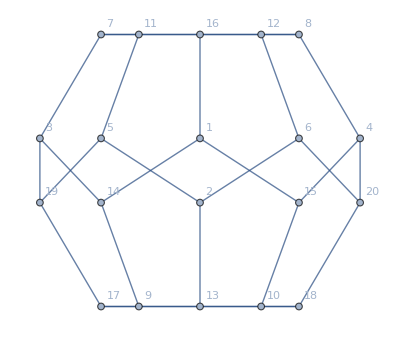

```mathematica
SetProperty[g,VertexCoordinates->%49]
```

### {1,0,GoldenRatio/2-1}

```mathematica
PolyhedronData["Dodecahedron","VertexCoordinates"][[1]]
```

{-√(1+2/(√5)),0,Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668}

```mathematica
v=FullSimplify[%/√(1+2/(√5))]
```

{-1,0,1/4 (3-√5)}

```mathematica
N[%]
```

{-1.,0.,0.190983}

```mathematica
(1-GoldenRatio/2)
```

0.190983

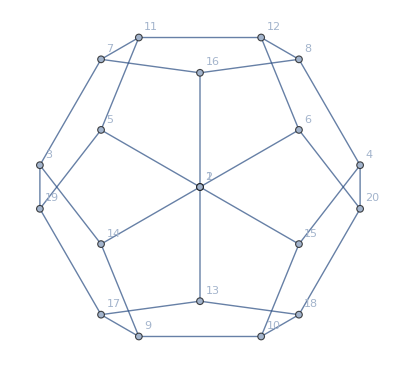

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{1,0,GoldenRatio/2-1,π/2},VertexLabels->"Name"]
```

### {XXX}

```mathematica
Mean[PolyhedronData["Dodecahedron","Faces"][[1]][[{1,3}]]]//FullSimplify
```

{-1/40 √(650+290 √5),1/8 (-3-√5),Root0.263Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668}

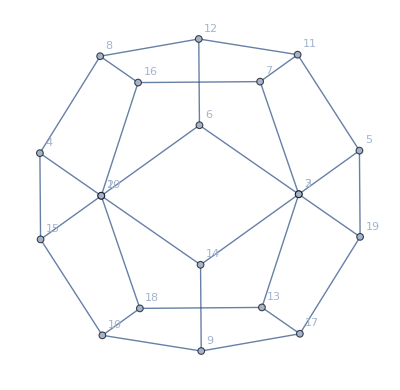

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{-1/40 √(650+290 √5),1/8 (-3-√5),Root"0.263"Root[1-20 #1^2+80 #1^4&,3]0.2628655560595668,π/10},VertexLabels->"Name"]
```

### {0, 1, 0}

```mathematica
<<MathWorld`Graphs`
```

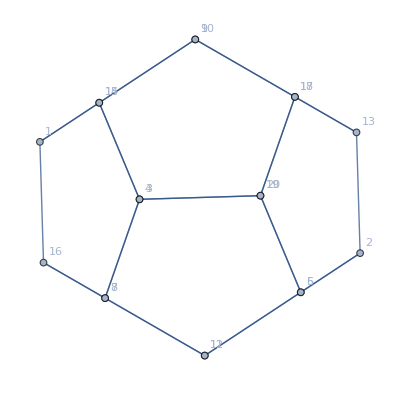

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{0,1,0,-π/6},VertexLabels->"Name"]
```

### {0, 0, 1}

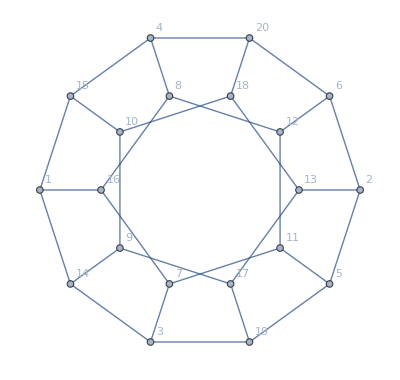

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{0,0,1},VertexLabels->"Name"]
```

### {1, 0, 1}

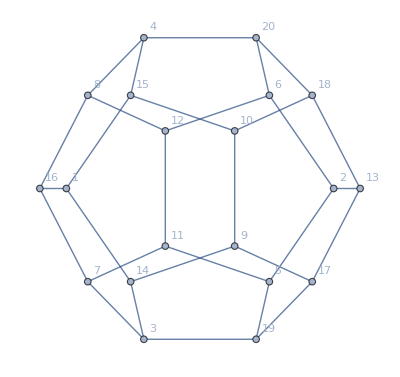

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{1,0,1},VertexLabels->"Name"]
```

### {1, 0, -1}

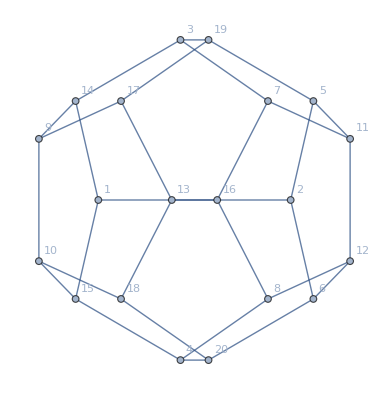

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{1,0,-1},VertexLabels->"Name"]
```

### {1.,5/2,5/2,-π/8}

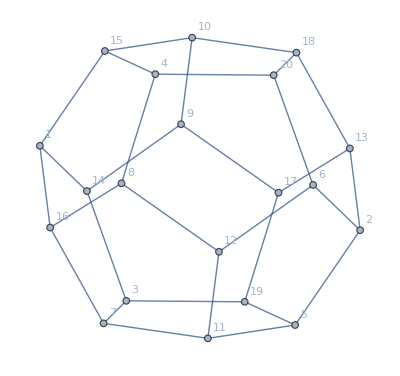

```mathematica
PolyhedronProjectionGraph[PolyhedronData["Dodecahedron","Polyhedron"],{1.,5/2,5/2,-π/8},VertexLabels->"Name"]
```

## Stereoscopic projections

```mathematica
PolyhedronData["Dodecahedron","Orientations"]
```

{C2,C3,C5}

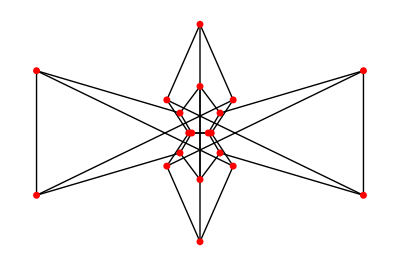
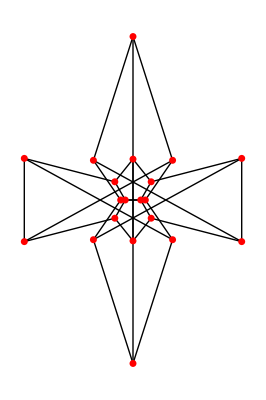
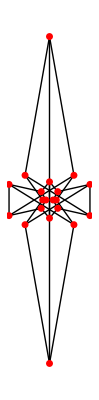
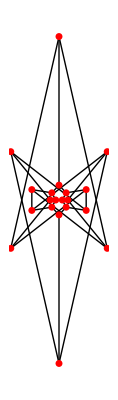
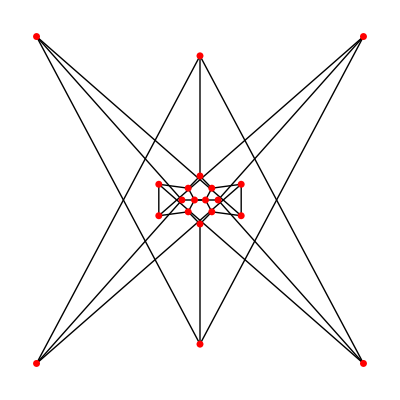
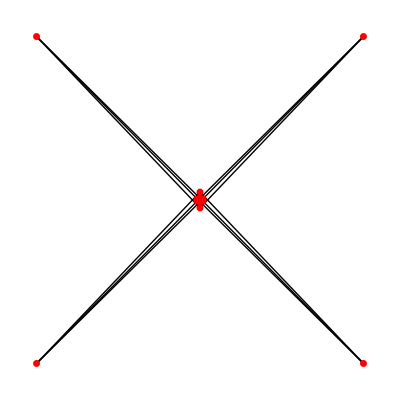
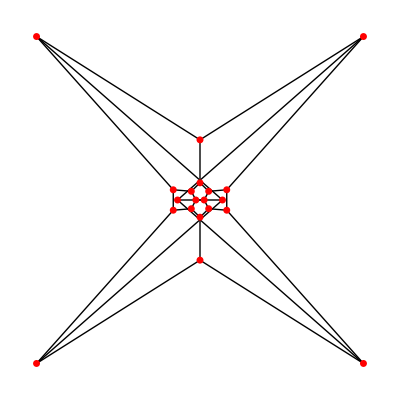
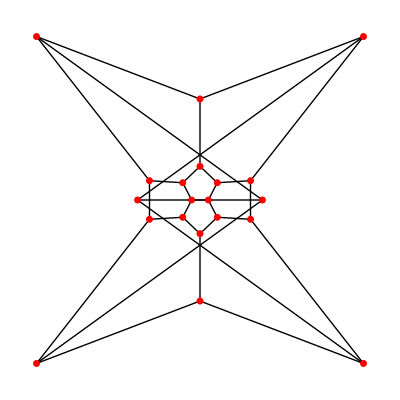
{-Graphics-,-Graphics-,-Graphics-,GraphPlot[⁃Graph:<30,20,Undirected>⁃,Method→None],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Quiet@GraphPlot[SkeletonGraph[PolyhedronData[{"Dodecahedron","C2"},"Faces"]//Normal,#],Method->None]&/@Range[.2,1.5,.1]
```

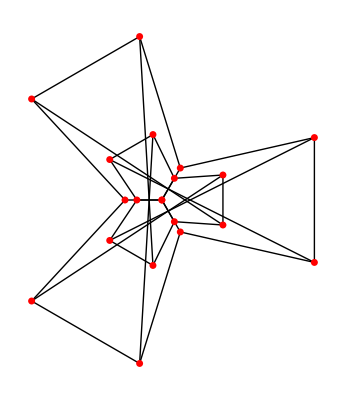
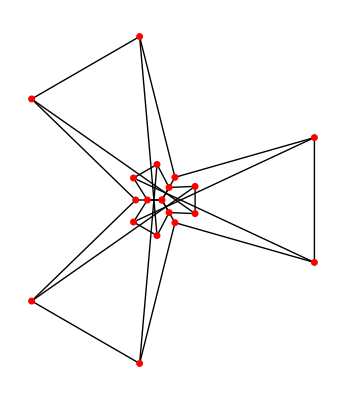
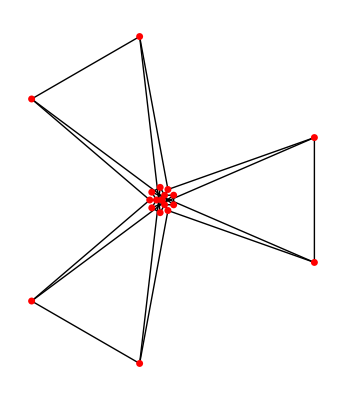
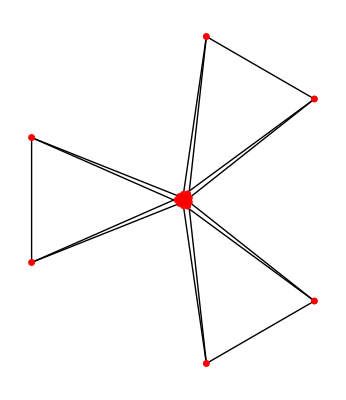
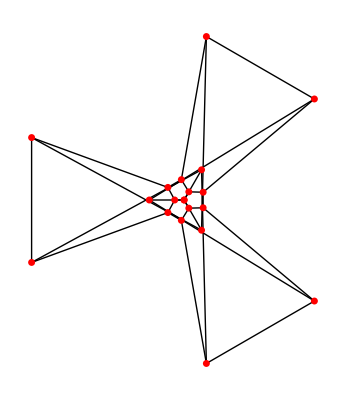
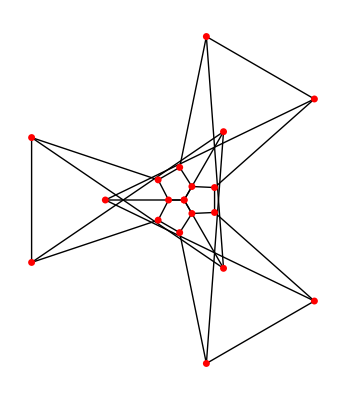
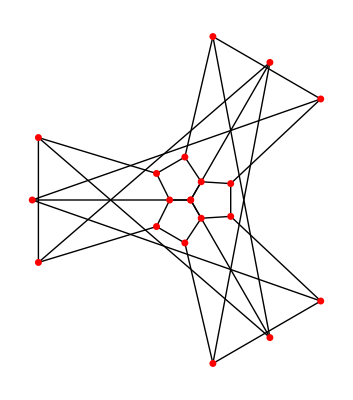
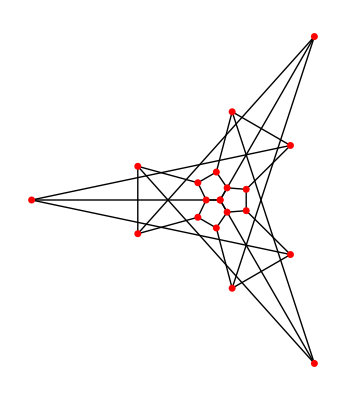

```mathematica
GraphPlot[SkeletonGraph[PolyhedronData[{"Dodecahedron","C3"},"Faces"]//Normal,#],Method->None]&/@Range[.2,2,.1]
```

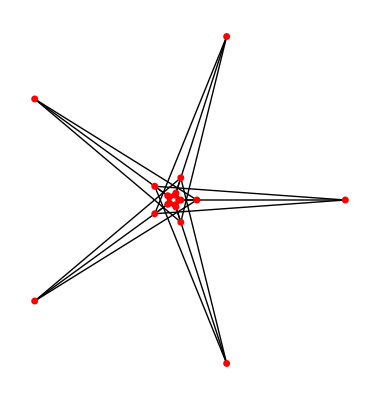
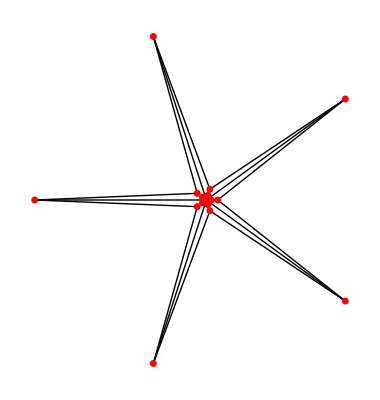
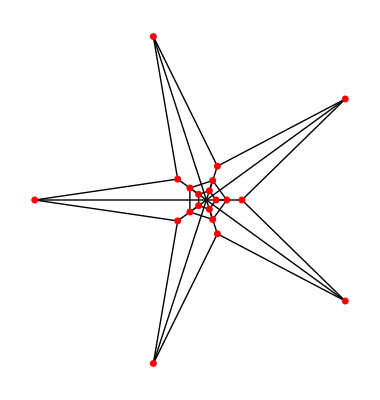
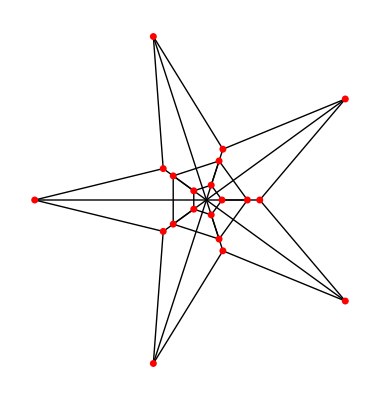
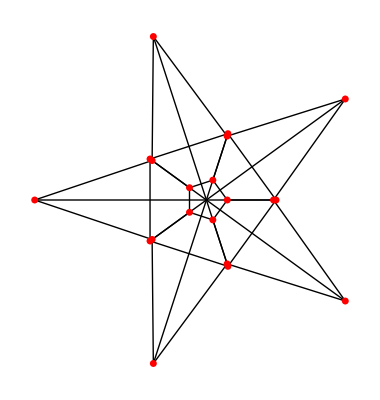
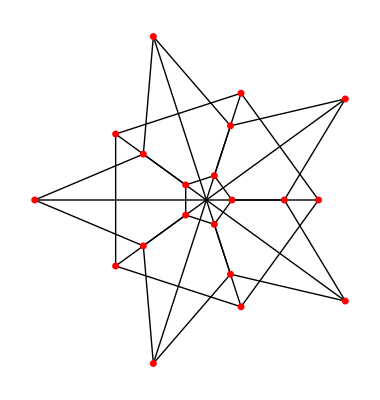
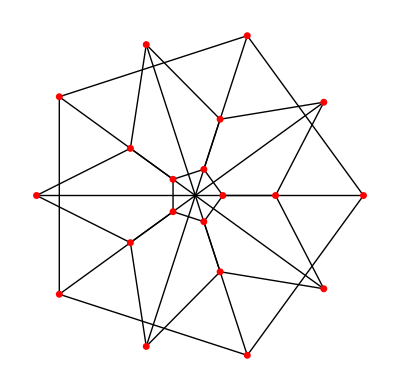
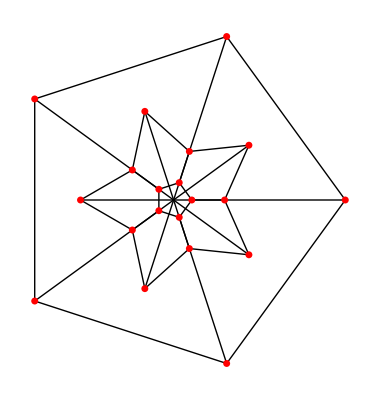

```mathematica
Quiet@GraphPlot[SkeletonGraph[PolyhedronData[{"Dodecahedron","C5"},"Faces"]//Normal,#],Method->None]&/@Range[.2,1.5,.1]
```

## Properties

### Classes

```mathematica
GraphData["DodecahedralGraph","Classes"]
```

{Biconnected,Bridgeless,Class1,CompletelyRegular,Connected,Cubic,DeterminedBySpectrum,DistanceRegular,EdgeTransitive,GeneralizedPetersen,Hamiltonian,LCF,Noneulerian,Planar,Platonic,Polyhedral,Regular,SquareFree,Symmetric,Traceable,TriangleFree,Unitransitive,VertexTransitive,WeaklyRegular}

### Matrices

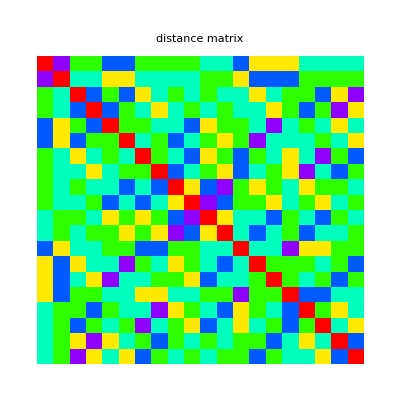

```mathematica
GraphicsRow[GraphMatrixPlot[GraphData["DodecahedralGraph"]]]
```

### Properties

```mathematica
TableForm[GraphDataTable["DodecahedralGraph",x],TableDepth->2]//TraditionalForm
```

GraphData::notdef: GraphData has no defined value for the specified tag or properties.

automorphism group order | 120
characteristic polynomial | (x-3) (x-1)^5 x^4 (x+2)^4 (x^2-5)^3
chromatic number | 3
chromatic polynomial | (x-2) (x-1) x (x^17-27 x^16+352 x^15-2950 x^14+17839 x^13-82777 x^12+305866 x^11-921448 x^10+2297495 x^9-4783425 x^8+8347700 x^7-12195590 x^6+14808795 x^5-14713381 x^4+11613602 x^3-6892084 x^2+2751604 x-555984)
circulant graph | Circulant
claw-free | N
clique number | 2
graph complement name | {GraphData[—,Name]}
cospectral graph names | ---
determined by spectrum | Y
diameter | 5
distance-regular graph | Y
dual graph name | {icosahedral graph}
edge chromatic number | 3
edge connectivity | 3
edge count | 30
Eulerian | N
generalized Petersen graph | {Gp8,10 | 2}
girth | 5
Hamiltonian | Y
Hamiltonian cycle count | 60
Hamiltonian path count | ?
integral graph | N
independence number | 8
LCF notation | {-10,-4,7,-7,4,-10,7,4,-4,-7} | 2
line graph | ?
line graph name | {icosidodecahedral graph}
perfect matching graph | N
planar | Y
polyhedral graph | Y
polyhedron embedding names | dodecahedron
great stellated dodecahedron
radius | 5
regular | Y
spectrum | (-√5)^3 (-2)^4 0^4 1^5 (√5)^3 3^1
square-free | Y
strongly regular parameters | StronglyRegular
traceable | Y
triangle-free | Y
vertex connectivity | 3
vertex count | 20
weakly regular parameters | {20,{3},{0},{0,1}}

## Graceful labelings

```mathematica
GraphData["DodecahedralGraph","Graceful"]
```

True

```mathematica
GraphData["DodecahedralGraph","GracefulLabelings"]
```

Missing[TooLarge,{0,20,1,17,8,26,3,14,23,2,12,4,5,30,18,28,10,29,27,6}]

```mathematica
lab=%[[2]]
```

{0,20,1,17,8,26,3,14,23,2,12,4,5,30,18,28,10,29,27,6}

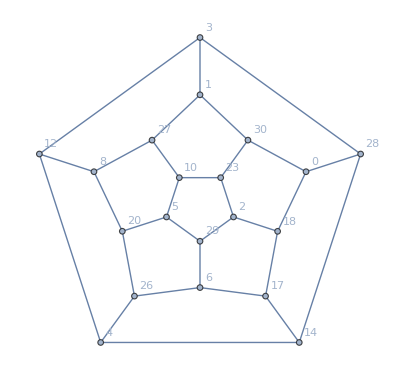

```mathematica
SetProperty[GraphData["DodecahedralGraph"],VertexLabels->Thread[Range[20]->lab]]
```

```mathematica
GracefullyLabeledGraphQ[%]
```

True

### Partial population

Bert Dobbelaere 2020-10-06:

Over 12 million "fundamentally different" solutions after running overnight.  I estimate the program could run for a month or so.

```mathematica
adj=1+{{1,4,5},{0,2,7},{1,3,9},{2,4,11},{0,3,13},{0,6,14},{5,7,15},{1,6,8},{7,9,16},{2,8,10},{9,11,17},{3,10,12},{11,13,19},{4,12,14},{5,13,18},{6,16,18},{8,15,17},{10,16,19},{14,15,19},{12,17,18}};
```

```mathematica
r=RecognizeGraph@(dodec=FromAdjacencyLists1[adj])
```

DodecahedralGraph

```mathematica
iso=FindGraphIsomorphism[GraphData[r],dodec][[1]]
```

<|1→1,2→18,3→3,4→15,5→11,6→20,7→4,8→14,9→8,10→7,11→12,12→13,13→17,14→2,15→6,16→5,17→9,18→16,19→10,20→19|>

```mathematica
vorder=Normal[iso][[All,2]]
```

{1,18,3,15,11,20,4,14,8,7,12,13,17,2,6,5,9,16,10,19}

```mathematica
vlab={0,30,1,3,28,18,2,23,10,27,8,12,4,14,17,29,5,20,6,26}[[vorder]]
```

{0,20,1,17,8,26,3,14,23,2,12,4,5,30,18,28,10,29,27,6}

```mathematica
glab=SetProperty[GraphData[r],VertexLabels->Thread[Range[20]->vlab]]
```

-Graphics-

```mathematica
GracefullyLabeledGraphQ[glab]
```

True

#### Full computation

On 10/21/20 12:50 PM, Bert Dobbelaere wrote:

> I couldn't resist starting the dodecahedron run anyway, split in multiple ranges so I could compute them in parallel.
> 
> The total number of graceful labelings I obtained for the dodecahedral graph is 784298856 * 240 = 188231725440.
> 
> Quite a number compared to the icosahedron...

```mathematica
2GraphData["DodecahedralGraph","AutomorphismCount"]
```

240

## Construction

### distanceregular.org

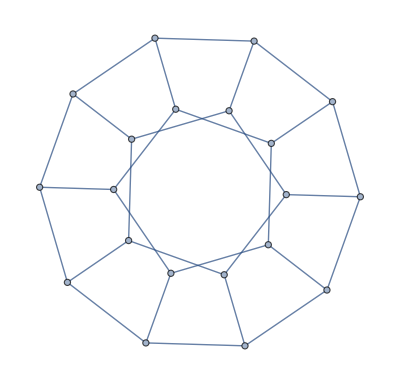

```mathematica
g=DistanceRegularGraph["http://www.distanceregular.org/graphdata/dodecahedron.am"]
```

```mathematica
ToEntity[g]
```

dodecahedral graph

```mathematica
VertexCount[g]
```

20

```mathematica
GraphDiameter[g]//Timing
```

{0.000051,5}

```mathematica
RegularParameters[g]//Timing
```

{0.003891,{20,{3},{0},{0,1}}}

```mathematica
DistanceRegularGraphQ[g]//Timing
```

{0.061212,True}

```mathematica
IntersectionArray[g]//Timing
```

{0.060375,{{3,2,1,1,1},{1,1,1,2,3}}}

```mathematica
IntegerSpectrum[g]//SpectrumForm
```

(-√5)^3 (-2)^4 0^4 1^5 (√5)^3 3^1

```mathematica
GroupOrder[GraphAutomorphismGroup[g]]
```

120

```mathematica
HamiltonianGraphQ[g]
```

True

### MinimalPlanarIntegral [old]

```mathematica
v={{405.799,20.1835},{1261.27,76.588},{1480.62,919.522},{750.493,1389.56},{79.9064,838.049},{446.536,51.5194},{1258.13,132.993},{1417.95,925.789},{719.157,1333.15},{114.376,800.446},{418.333,490.221},{828.833,230.134},{1201.73,549.759},{1010.58,1010.4},{509.207,975.926},{528.009,903.854},{484.139,465.152},{869.569,289.672},{1167.26,612.431},{944.775,988.461}};
```

```mathematica
Length[v]
```

20

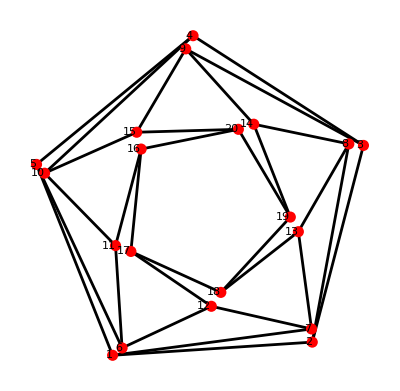

```mathematica
ShowLabeledGraph[g=Graph[List/@{
Sequence@@Partition[Range[5],2,1,1],
Sequence@@Partition[Range[16,20],2,1,1],
{1,7},{7,13},{13,8},{4,10},{9,15},{15,10},{10,11},{11,6},{6,12},{12,7},{12,17},{18,13},{14,8},{9,14},{15,20},{16,11},{14,19},{2,8},{3,9},{5,6}
},List/@v],VertexStyle->Disk[.02]]
```

```mathematica
Degrees[g]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
RecognizeGraph[g]
```

DodecahedralGraph

```mathematica
θ=ArcTan@@Subtract@@v[[{2,1}]]
```

0.0658386

```mathematica
v=Vertices[g];
```

```mathematica
s=Norm[Subtract@@v[[{2,1}]]]
```

857.328

```mathematica
v2=RotationMatrix[-θ].#&/@(2/s(#-v[[1]])&/@v)
```

{{0.,0.},{2.,0.},{2.63997,1.92849},{1.01254,3.1347},{-0.633079,1.95382},{0.0996359,0.0666906},{2.00135,0.13178},{2.49505,1.9527},{0.93094,3.0082},{-0.558613,1.861},{0.101317,1.09222},{1.01695,0.42379},{1.93403,1.11057},{1.55977,2.21218},{0.387397,2.20888},{0.420102,2.03823},{0.250651,1.02376},{1.12091,0.556129},{1.86341,1.26175},{1.40322,2.17121}}

```mathematica
c=Mean[Take[v2,5]]
```

{1.00389,1.4034}

```mathematica
v3=(#-c)&/@v2
```

{{-1.00389,-1.4034},{0.996114,-1.4034},{1.63608,0.525091},{0.00865412,1.73129},{-1.63697,0.550421},{-0.90425,-1.33671},{0.997462,-1.27162},{1.49116,0.549298},{-0.0729468,1.60479},{-1.5625,0.457599},{-0.902569,-0.311185},{0.0130643,-0.979612},{0.93014,-0.292829},{0.555885,0.808776},{-0.616489,0.805479},{-0.583784,0.634826},{-0.753235,-0.37964},{0.117026,-0.847273},{0.85952,-0.141653},{0.399338,0.767807}}

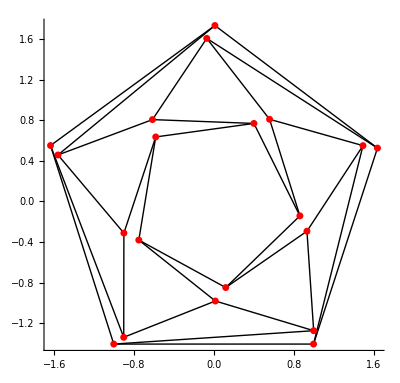

```mathematica
GraphPlot[g2=ChangeVertices[g,v3],Method->None,Axes->True]
```

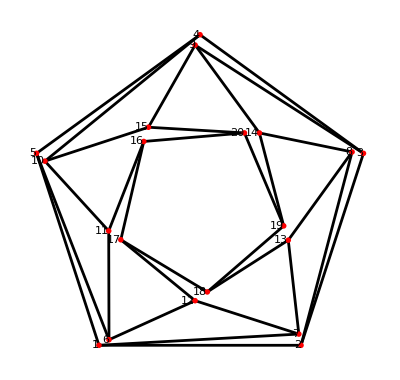

```mathematica
With[{
θ=-1.8,ϕ=.03,ψ=-.68,
r=1.1,R=.94
},ShowLabeledGraph[g3=ChangeVertices[g2,Join[
Table[Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5]],{k,5}],
Table[R Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ϕ]],{k,5}],
Table[1/2 r Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ψ]],{k,5}],
Table[1/2 Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+θ]],{k,5}]
]
],VertexStyle->Disk[.01]]]
```

```mathematica
g3//InputForm
```

Graph[{{{1, 2}}, {{2, 3}}, {{3, 4}}, {{4, 5}}, {{5, 1}}, {{16, 17}}, {{17, 18}}, {{18, 19}}, {{19, 20}}, 
  {{20, 16}}, {{1, 7}}, {{7, 13}}, {{13, 8}}, {{4, 10}}, {{9, 15}}, {{15, 10}}, {{10, 11}}, {{11, 6}}, 
  {{6, 12}}, {{12, 7}}, {{12, 17}}, {{18, 13}}, {{14, 8}}, {{9, 14}}, {{15, 20}}, {{16, 11}}, {{14, 19}}, 
  {{2, 8}}, {{3, 9}}, {{5, 6}}}, {{{-1, (-1 - Sqrt[5])/(4*Sqrt[5/8 - Sqrt[5]/8])}}, 
  {{1, (-1 - Sqrt[5])/(4*Sqrt[5/8 - Sqrt[5]/8])}}, 
  {{Sqrt[(5/8 + Sqrt[5]/8)/(5/8 - Sqrt[5]/8)], (-1 + Sqrt[5])/(4*Sqrt[5/8 - Sqrt[5]/8])}}, 
  {{0, 1/Sqrt[5/8 - Sqrt[5]/8]}}, {{-Sqrt[(5/8 + Sqrt[5]/8)/(5/8 - Sqrt[5]/8)], 
    (-1 + Sqrt[5])/(4*Sqrt[5/8 - Sqrt[5]/8])}}, {{-0.9007688834002959, -1.321412609545296}}, 
  {{0.9783851800477993, -1.265021069164605}}, {{1.5054441787590225, 0.5395865923168378}}, 
  {{-0.047969509409050703, 1.5985039230901437}}, {{-1.5350909659974739, 0.448343163302919}}, 
  {{-0.9036676378005895, -0.24279420435705867}}, {{-0.04833764717456861, -0.9344665307773743}}, 
  {{0.8737933289105058, -0.33473787301255803}}, {{0.5883716235841774, 0.7275871479337672}}, 
  {{-0.5101596675195248, 0.7844114602132242}}, {{-0.5565920888706728, 0.6432822431534698}}, 
  {{-0.7837941835637598, -0.33056538772472527}}, {{0.07218064324379499, -0.8475828882716374}}, 
  {{0.8284042744182557, -0.19326964550995132}}, {{0.4398013547723822, 0.7281356783528439}}}]

```mathematica
v=Vertices[g3];
Norm[Subtract@@v[[#]]]&/@Edges[g3]//FullSimplify
```

{2,2,2,2,2,1.,1.,1.,1.,1.,1.98152,0.936144,1.07862,1.98152,0.936144,1.07862,0.936144,1.07862,0.936144,1.07862,0.951626,0.951626,0.936144,1.07862,0.951626,0.951626,0.951626,1.98152,1.98152,1.98152}

```mathematica
vv=Join[
Table[Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5]],{k,5}],
Table[R Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ϕ]],{k,5}],
Table[1/2 r Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ψ]],{k,5}],
Table[1/2 Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+θ]],{k,5}]
]/.ϕ->π/100
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0,1/(√(5/8-(√5)/8))},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{-(R Sin[(19 π)/100])/(√(5/8-(√5)/8)),-(R Cos[(19 π)/100])/(√(5/8-(√5)/8))},{(R Sin[(21 π)/100])/(√(5/8-(√5)/8)),-(R Cos[(21 π)/100])/(√(5/8-(√5)/8))},{(R Cos[(11 π)/100])/(√(5/8-(√5)/8)),(R Sin[(11 π)/100])/(√(5/8-(√5)/8))},{-(R Sin[π/100])/(√(5/8-(√5)/8)),(R Cos[π/100])/(√(5/8-(√5)/8))},{-(R Cos[(9 π)/100])/(√(5/8-(√5)/8)),(R Sin[(9 π)/100])/(√(5/8-(√5)/8))},{-(r Sin[π/5-ψ])/(2 √(5/8-(√5)/8)),-(r Cos[π/5-ψ])/(2 √(5/8-(√5)/8))},{(r Sin[π/5+ψ])/(2 √(5/8-(√5)/8)),-(r Cos[π/5+ψ])/(2 √(5/8-(√5)/8))},{(r Cos[π/10+ψ])/(2 √(5/8-(√5)/8)),(r Sin[π/10+ψ])/(2 √(5/8-(√5)/8))},{-(r Sin[ψ])/(2 √(5/8-(√5)/8)),(r Cos[ψ])/(2 √(5/8-(√5)/8))},{-(r Cos[π/10-ψ])/(2 √(5/8-(√5)/8)),(r Sin[π/10-ψ])/(2 √(5/8-(√5)/8))},{-Sin[π/5-θ]/(2 √(5/8-(√5)/8)),-Cos[π/5-θ]/(2 √(5/8-(√5)/8))},{Sin[π/5+θ]/(2 √(5/8-(√5)/8)),-Cos[π/5+θ]/(2 √(5/8-(√5)/8))},{Cos[π/10+θ]/(2 √(5/8-(√5)/8)),Sin[π/10+θ]/(2 √(5/8-(√5)/8))},{-Sin[θ]/(2 √(5/8-(√5)/8)),Cos[θ]/(2 √(5/8-(√5)/8))},{-Cos[π/10-θ]/(2 √(5/8-(√5)/8)),Sin[π/10-θ]/(2 √(5/8-(√5)/8))}}

```mathematica
n[x_,y_]:=#.#&[vv[[x]]-vv[[y]]]
```

#### FindRoot

```mathematica
soln=FindRoot[{
(*n[9,14]==1,*)
n[4,10]==2^2,
n[20,15]==1,
n[10,15]==1,
n[14,8]==1 (* added *)
},{θ,-1.8,-1.9},{ψ,-.68,-.7},
{r,1.1,1.2},{R,.94,.96},MaxIterations->10^4,WorkingPrecision->50]
```

{θ→-1.7056097879257796103860159614608375667124365057503,ψ→-0.59690260418206071530790224282310554799754850595297,r→1.2078694436200308472764689180896917605187159914163,R→0.95707815686611063222867711536412461546114343529005}

```mathematica
Select[Edges[g3],Norm[Subtract@@Vertices[g3][[#]]]<.95&]
```

{{7,13},{9,15},{10,11},{6,12},{14,8}}

```mathematica
vnew=vv/.soln;
```

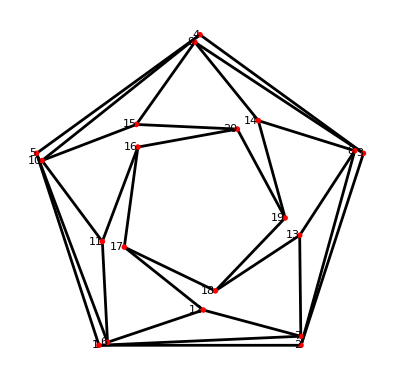

```mathematica
ShowLabeledGraph[g4=ChangeVertices[g3,vnew],VertexStyle->Disk[.01]]
```

```mathematica
s=Norm[Subtract@@vnew[[#]]]&/@Edges[g4]//FullSimplify
```

{2,2,2,2,2,1.,1.,1.,1.,1.,2.,0.99999999999999999999999999999999999999969546852,0.9999999999999999999999999999999999999998652383422,2.,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999998652383422,0.9999999999999999999999999999999999999996954685151,0.999999999999999999999999999999999999999865238342,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999998652383422,1.000000000000000000000000000000000000000018906767,1.000000000000000000000000000000000000000018906767,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999998652383422,1.00000000000000000000000000000000000000001890677,1.000000000000000000000000000000000000000018906767,1.000000000000000000000000000000000000000018906767,2.,2.,2.}

```mathematica
ToCommonEdges[g4,"DodecahedralGraph"]//N
```

{{-1.,-1.37638},{0.369217,0.766346},{0.,1.7013},{0.986678,-0.286656},{-0.629747,0.811865},{0.842932,-0.114332},{1.61803,0.525731},{1.53202,0.55156},{-0.915228,-1.34672},{0.0322738,-1.02697},{-0.0511455,1.62748},{0.577527,0.849805},{-0.614744,0.58796},{-1.61803,0.525731},{0.997983,-1.28659},{1.,-1.37638},{-0.966732,-0.348045},{-0.749149,-0.402967},{-1.56363,0.454275},{0.151744,-0.837007}}

#### Equations

```mathematica
{ϕ->π/100,
θ->-1.70560978792577961038601596146083756671243650575033830256890571236629180161806`50.,ψ->-0.59690260418206071530790224282310554799754850595296608734085729074044126728344`50.,r->1.20786944362003084727646891808969176051871599141625694902742932477722499564001`50.,R->0.95707815686611063222867711536412461546114343529004809765978406494528295603317`50.}
```

```mathematica
Through[{Cos,Sin}[-1.70560978792577961038601596146083756671243650575033830256890571236629180161806`50.]]
```

{-0.134405467053038180890544532701286326871842659538,-0.9909264202887390306794769363027335736894030068316}

```mathematica
Through[{Cos,Sin}[-0.59690260418206071530790224282310554799754850595296608734085729074044126728344`50]]
```

{0.82708057427456182491785218621532942556305115316037,-0.56208337785213060009725200130888835384301671523477}

```mathematica
eqn=FullSimplify[TrigExpand@{
n[4,10]==2^2,
n[20,15]==1,
n[10,15]==1,
n[14,8]==1
}/.{Cos[θ]->u,Sin[θ]->-√(1-u^2),Cos[ψ]->v,Sin[ψ]->-√(1-v^2)}]
```

{√5+2 R (R-2 Sin[(9 π)/100])==3,√5+2 r (r-2 (u v+√(1-u^2) √(1-v^2)))==3,√5+8 R^2+2 r (r-4 R v Cos[π/100]+4 R √(1-v^2) Sin[π/100])==5,√5+8 R^2+2 r (r-4 R (√(1-v^2) Cos[(11 π)/100]+v Sin[(11 π)/100]))==5}

#### NSolve π/100

```mathematica
soln=NSolve[eqn,{u,v,r,R},Reals]
```

```mathematica
soln={{R->-0.3990959447876521,v->0.8270805742745618,r->0.4321405727249934,u->-0.7343747174881446},{R->-0.3990959447876521,v->0.8270805742745606,r->-1.7236421796023367,u->-0.9922859882503167},{R->0.9570781568661106,v->0.827080574274562,r->1.8893005317789116,u->0.39583991014193765},{R->0.9570781568661106,v->0.827080574274562,r->1.8893005317789116,u->0.9995502986010655},{R->0.9570781568661106,v->0.827080574274562,r->1.2078694436200312,u->-0.13440546705303744}};
```

```mathematica
soln[[-1]]
```

{R→0.957078,v→0.827081,r→1.20787,u→-0.134405}

```mathematica
{θ->ArcCos[u],ψ->ArcCos[v]}/.soln[[-1]]
```

{θ→1.70561,ψ→0.596903}

```mathematica
r=.
```

```mathematica
vv/.{θ->ArcCos[u],ψ->ArcCos[v]}/.soln[[1]]
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0,1/(√(5/8-(√5)/8))},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0.381645,0.561573},{-0.416153,0.536501},{-0.638842,-0.229997},{0.0213274,-0.678648},{0.652023,-0.18943},{-0.0115466,-0.367419},{0.345868,-0.12452},{0.225305,0.290462},{-0.206622,0.304035},{-0.353005,-0.102557},{0.834293,0.166018},{0.0999183,0.844762},{-0.77254,0.356074},{-0.577374,-0.624696},{0.415703,-0.742157}}

```mathematica
e=Select[Subsets[Range[20],{2}],Abs[Round[d=EuclideanDistance@@(vv[[#]]/.{θ->-ArcCos[u],ψ->-ArcCos[v]}/.soln[[-1]])]-d]<=1*^-2&]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-√((-1+√Times[«2»])^2+(-1/4 Plus[«2»] Power[«2»]+1/4 Power[«2»] Plus[«2»])^2).

Norm::nvm: The first Norm argument should be a scalar, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-√((-1+√Times[«2»])^2+(-1/4 Plus[«2»] Power[«2»]+1/4 Power[«2»] Plus[«2»])^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-√((5/8+1/8 Power[«2»])/(5/8+Times[«2»])+(1/(√Plus[«2»])-1/4 Power[«2»] Plus[«2»])^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{{1,2},{1,5},{1,7},{1,16},{1,17},{2,3},{2,8},{2,17},{2,18},{3,4},{3,9},{3,18},{3,19},{4,5},{4,10},{4,19},{4,20},{5,6},{5,16},{5,20},{16,17},{16,20},{17,18},{18,19},{19,20}}

```mathematica
e2={{1,2},{1,5},{1,7},{2,3},{2,8},{3,4},{3,9},{4,5},{4,10},{5,6},{6,11},{6,12},{7,12},{7,13},{8,13},{8,14},{9,14},{9,15},{10,11},{10,15},{11,16},{12,17},{13,18},{14,19},{15,20},{16,17},{16,20},{17,18},{18,19},{19,20}};
```

```mathematica
vc=(vv/.{θ->-ArcCos[u],ψ->-ArcCos[v]}/.soln[[-1]])
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0,1/(√(5/8-(√5)/8))},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{-0.915228,-1.34672},{0.997983,-1.28659},{1.53202,0.55156},{-0.0511455,1.62748},{-1.56363,0.454275},{-0.966732,-0.348045},{0.0322738,-1.02697},{0.986678,-0.286656},{0.577527,0.849805},{-0.629747,0.811865},{-0.614744,0.58796},{-0.749149,-0.402967},{0.151744,-0.837007},{0.842932,-0.114332},{0.369217,0.766346}}

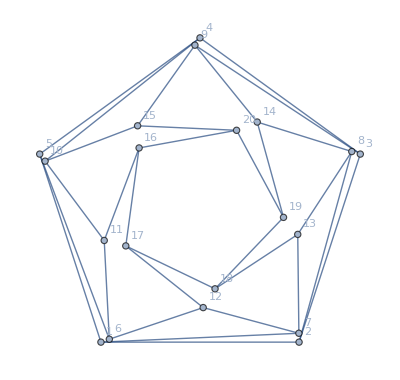

```mathematica
g=Graph[Range[20],UndirectedEdge@@@e2,VertexCoordinates->vc,VertexLabels->"Name"]
```

```mathematica
RecognizeGraph[g]
```

Reading CanonicalForms from raw GraphData file cache (first time only)...

Reading GraphData standard names from raw GraphData file cache (first time only)...

Building default Association of length 10589...

DodecahedralGraph

```mathematica
EdgeLengths[g]//FullSimplify
```

{2,2,2.,2,2.,2,2.,2,2.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

#### NSolve ArcSin[1/32]

```mathematica
π/100.
```

0.0314159

```mathematica
Convergents[Sin[π/100],5]
```

{0,1/31,1/32,6/191,55/1751}

```mathematica
vv=Join[
Table[Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5]],{k,5}],
Table[R Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ϕ]],{k,5}],
Table[1/2 r Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ψ]],{k,5}],
Table[1/2 Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+θ]],{k,5}]
]/.ϕ->ArcSin[1/32]
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0,1/(√(5/8-(√5)/8))},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{-(R Sin[π/5-ArcSin[1/32]])/(√(5/8-(√5)/8)),-(R Cos[π/5-ArcSin[1/32]])/(√(5/8-(√5)/8))},{(R Sin[π/5+ArcSin[1/32]])/(√(5/8-(√5)/8)),-(R Cos[π/5+ArcSin[1/32]])/(√(5/8-(√5)/8))},{(R Cos[π/10+ArcSin[1/32]])/(√(5/8-(√5)/8)),(R Sin[π/10+ArcSin[1/32]])/(√(5/8-(√5)/8))},{-R/(32 √(5/8-(√5)/8)),1/32 √(1023/(5/8-(√5)/8)) R},{-(R Cos[π/10-ArcSin[1/32]])/(√(5/8-(√5)/8)),(R Sin[π/10-ArcSin[1/32]])/(√(5/8-(√5)/8))},{-(r Sin[π/5-ψ])/(2 √(5/8-(√5)/8)),-(r Cos[π/5-ψ])/(2 √(5/8-(√5)/8))},{(r Sin[π/5+ψ])/(2 √(5/8-(√5)/8)),-(r Cos[π/5+ψ])/(2 √(5/8-(√5)/8))},{(r Cos[π/10+ψ])/(2 √(5/8-(√5)/8)),(r Sin[π/10+ψ])/(2 √(5/8-(√5)/8))},{-(r Sin[ψ])/(2 √(5/8-(√5)/8)),(r Cos[ψ])/(2 √(5/8-(√5)/8))},{-(r Cos[π/10-ψ])/(2 √(5/8-(√5)/8)),(r Sin[π/10-ψ])/(2 √(5/8-(√5)/8))},{-Sin[π/5-θ]/(2 √(5/8-(√5)/8)),-Cos[π/5-θ]/(2 √(5/8-(√5)/8))},{Sin[π/5+θ]/(2 √(5/8-(√5)/8)),-Cos[π/5+θ]/(2 √(5/8-(√5)/8))},{Cos[π/10+θ]/(2 √(5/8-(√5)/8)),Sin[π/10+θ]/(2 √(5/8-(√5)/8))},{-Sin[θ]/(2 √(5/8-(√5)/8)),Cos[θ]/(2 √(5/8-(√5)/8))},{-Cos[π/10-θ]/(2 √(5/8-(√5)/8)),Sin[π/10-θ]/(2 √(5/8-(√5)/8))}}

```mathematica
eqn=FullSimplify[TrigExpand@{
n[4,10]==2^2,
n[20,15]==1,
n[10,15]==1,
n[14,8]==1
}/.{Cos[θ]->u,Sin[θ]->-√(1-u^2),Cos[ψ]->v,Sin[ψ]->-√(1-v^2)}]
```

{√1023 (-1+√5) R==32 (-3+√5)+R (√(2 (5+√5))+64 R),√5+2 r (r-2 (u v+√(1-u^2) √(1-v^2)))==3,8 r^2+4 (√5+8 R^2)+r R √(1-v^2)==20+√1023 r R v,16 (-5+√5+8 R^2)+r (32 r-(√1023 (-1+√5)+√(2 (5+√5))) R v+(-1+√5-√(2046 (5+√5))) R √(1-v^2))==0}

```mathematica
soln=NSolve[eqn,{u,v,r,R},Reals]
```

{{R→-0.399005,v→0.82699,r→0.432334,u→-0.734279},{R→-0.399005,v→0.82699,r→-1.72354,u→-0.992295},{R→0.957296,v→0.82699,r→1.88881,u→0.395224},{R→0.957296,v→0.82699,r→1.88881,u→0.999561},{R→0.957296,v→0.82699,r→1.20907,u→-0.133727}}

```mathematica
vc=(vv/.{θ->-ArcCos[u],ψ->-ArcCos[v]}/.soln[[-1]])
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0,1/(√(5/8-(√5)/8))},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{-0.915653,-1.34688},{0.998004,-1.28705},{1.53245,0.551439},{-0.0508953,1.62785},{-1.56391,0.45463},{-0.967748,-0.348235},{0.0321405,-1.02799},{0.987612,-0.2871},{0.578237,0.850556},{-0.630242,0.812773},{-0.615147,0.587539},{-0.748873,-0.40348},{0.152318,-0.836903},{0.84301,-0.113755},{0.368692,0.766599}}

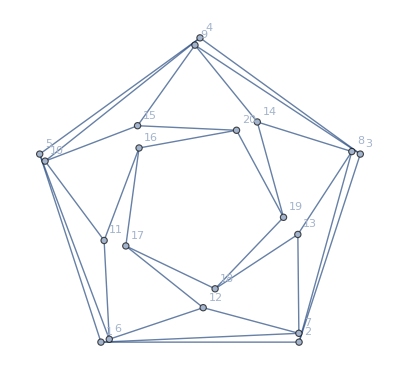

```mathematica
g=Graph[Range[20],UndirectedEdge@@@e2,VertexCoordinates->vc,VertexLabels->"Name"]
```

```mathematica
RecognizeGraph[g]
```

DodecahedralGraph

```mathematica
EdgeLengths[g]//FullSimplify
```

{2,2,2.,2,2.,2,2.,2,2.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

#### Solve

```mathematica
eqn//Column
```

√1023 (-1+√5) R==32 (-3+√5)+R (√(2 (5+√5))+64 R)
√5+2 r (r-2 (u v+√(1-u^2) √(1-v^2)))==3
8 r^2+4 (√5+8 R^2)+r R √(1-v^2)==20+√1023 r R v
16 (-5+√5+8 R^2)+r (32 r-(√1023 (-1+√5)+√(2 (5+√5))) R v+(-1+√5-√(2046 (5+√5))) R √(1-v^2))==0

```mathematica
(soln=Solve[eqn,{u,v,r,R},Reals])//Timing
```

$Aborted

```mathematica
Solve[√1023 (-1+√5) R==32 (-3+√5)+R (√(2 (5+√5))+64 R),R,Reals]//FullSimplify
```

{{R→1/128 (√1023 (-1+√5)-√(2 (5+√5))-2 √(7681-2559 √5-√(2046 (5-√5))))},{R→1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5))))}}

```mathematica
N[%]
```

{{R→-0.399005},{R→0.957296}}

```mathematica
NSolve[eqn/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

{{u→0.395224,v→0.82699,r→1.88881},{u→-0.133727,v→0.82699,r→1.20907},{u→0.999561,v→0.82699,r→1.88881}}

```mathematica
NSolve[Append[eqn,u<0]/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

{{u→-0.133727,v→0.82699,r→1.20907}}

```mathematica
Solve[Append[eqn,u<0]/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

$Aborted

√1023 (-1+√5) R==32 (-3+√5)+R (√(2 (5+√5))+64 R)
√5+2 r (r-2 (u v+√(1-u^2) √(1-v^2)))==3
8 r^2+4 (√5+8 R^2)+r R √(1-v^2)==20+√1023 r R v
16 (-5+√5+8 R^2)+r (32 r-(√1023 (-1+√5)+√(2 (5+√5))) R v+(-1+√5-√(2046 (5+√5))) R √(1-v^2))==0

```mathematica
NSolve[{
 (1-u^2 )(1-v^2)==(1/2((3-√5)/(2r)-r)+u v)^2,
r^2 R^2 (1-v^2)==(20+√1023 r R v-(8 r^2+4 (√5+8 R^2)))^2,
16 (-5+√5+8 R^2)+r (32 r-(√1023 (-1+√5)+√(2 (5+√5))) R v+(-1+√5-√(2046 (5+√5))) R √(1-v^2))==0
}/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

{{v→0.809017,r→2.05589,u→0.548093},{v→0.809017,r→2.05589,u→0.96485},{v→0.82699,r→1.88881,u→0.395224},{v→0.82699,r→1.88881,u→0.999561},{v→0.82699,r→1.20907,u→-0.133727},{v→0.82699,r→1.20907,u→0.872355},{v→0.809017,r→1.11081,u→-0.232616},{v→0.809017,r→1.11081,u→0.853086}}

```mathematica
NSolve[{
 (1-u^2 )(1-v^2)==(1/2((3-√5)/(2r)-r)+u v)^2,
r^2 R^2 (1-v^2)==(20+√1023 r R v-(8 r^2+4 (√5+8 R^2)))^2,
 R^2 (1-v^2)==(((-16 (-5+√5+8 R^2))/r- 32 r+(√1023 (-1+√5)+√(2 (5+√5))) R v)/(-1+√5-√(2046 (5+√5))))^2
}/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

{{v→0.809017,r→2.05589,u→0.548093},{v→0.809017,r→2.05589,u→0.96485},{v→-0.809017,r→-2.05589,u→0.548093},{v→-0.809017,r→-2.05589,u→0.96485},{v→-0.82699,r→-1.88881,u→0.395224},{v→-0.82699,r→-1.88881,u→0.999561},{v→0.82699,r→1.88881,u→0.395224},{v→0.82699,r→1.88881,u→0.999561},{v→0.82699,r→1.20907,u→-0.133727},{v→0.82699,r→1.20907,u→0.872355},{v→-0.82699,r→-1.20907,u→-0.133727},{v→-0.82699,r→-1.20907,u→0.872355},{v→-0.809017,r→-1.11081,u→-0.232616},{v→-0.809017,r→-1.11081,u→0.853086},{v→0.809017,r→1.11081,u→-0.232616},{v→0.809017,r→1.11081,u→0.853086}}

```mathematica
FullSimplify[(((-16 (-5+√5+8 R^2))/r- 32 r+(√1023 (-1+√5)+√(2 (5+√5))) R v)/(-1+√5-√(2046 (5+√5))))^2]
```

((32 r+(16 (-5+√5+8 R^2))/r-(√1023 (-1+√5)+√(2 (5+√5))) R v)^2)/(1-√5+√(2046 (5+√5)))^2

```mathematica
NSolve[{
 (1-u^2 )(1-v^2)==(1/2((3-√5)/(2r)-r)+u v)^2,
r^2 R^2 (1-v^2)==(20+√1023 r R v-(8 r^2+4 (√5+8 R^2)))^2,
 R^2 (1-v^2)==((32 r+(16 (-5+√5+8 R^2))/r-(√1023 (-1+√5)+√(2 (5+√5))) R v)^2)/(1-√5+√(2046 (5+√5)))^2,
v>0,u<0,r>1.2
}/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

{{v→0.82699,r→1.20907,u→-0.133727}}

```mathematica
{v->0.8269901591903418,r->1.2090696436948747,u->-0.1337265555509568}}
```

```mathematica
Solve[{
 (1-u^2 )(1-v^2)==(1/2((3-√5)/(2r)-r)+u v)^2,
r^2 R^2 (1-v^2)==(20+√1023 r R v-(8 r^2+4 (√5+8 R^2)))^2,
(1-√5+√(2046 (5+√5)))^2 R^2 (1-v^2)==(32 r+(16 (-5+√5+8 R^2))/r-(√1023 (-1+√5)+√(2 (5+√5))) R v)^2,
v>0,u<0,r>1.2
}/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5)))),{u,v,r},Reals]
```

$Aborted

```mathematica
FullSimplify@RootReduce[{
 (1-u^2 )(1-v^2)==(1/2((3-√5)/(2r)-r)+u v)^2,
r^2 R^2 (1-v^2)==(20+√1023 r R v-(8 r^2+4 (√5+8 R^2)))^2,
(1-√5+√(2046 (5+√5)))^2 R^2 (1-v^2)==(32 r+(16 (-5+√5+8 R^2))/r-(√1023 (-1+√5)+√(2 (5+√5))) R v)^2
}/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5))))]
```

{(-1+u^2) (-1+v^2)==(-3+√5+2 r (r-2 u v))^2/(16 r^2),r^2 (-1+v^2) Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464==(-8 r^2+Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2,(-1+v^2) Root-1.33 × 10^4Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122==(32 r+(Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416)/r+v Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2}

```mathematica
(eqn3={16 r^2(-1+u^2) (-1+v^2)==(-3+√5+2 r (r-2 u v))^2,r^2 (-1+v^2) Root"-0.916"Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464==(-8 r^2+Root"-18.3"Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root"30.6"Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2,r^2(-1+v^2) Root"-1.33"" × "("10")^("4")Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122==(32 r^2+Root"73.1"Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416+v r Root"-41.5"Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2})//Column
```

16 r^2 (-1+u^2) (-1+v^2)==(-3+√5+2 r (r-2 u v))^2
r^2 (-1+v^2) Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464==(-8 r^2+Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2
r^2 (-1+v^2) Root-1.33 × 10^4Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122==(32 r^2+Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416+r v Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2

```mathematica
NSolve[Join[eqn3,{v>0,u<0,r>1.2}],{u,v,r},Reals]
```

{{v→0.82699,r→1.20907,u→-0.133727}}

```mathematica
Take[eqn3,-2]
```

{r^2 (-1+v^2) Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464==(-8 r^2+Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2,r^2 (-1+v^2) Root-1.33 × 10^4Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122==(32 r^2+Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416+r v Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2}

```mathematica
Solve[Join[
{
r^2 (-1+v^2) Root"-0.916"Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464==(-8 r^2+Root"-18.3"Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root"30.6"Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2,
r^2 (-1+v^2) Root"-1.33"" × "("10")^("4")Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122==(32 r^2+Root"73.1"Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416+r v Root"-41.5"Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2
},{v>0,r>1.2}],{r,v},Reals]
```

$Aborted

```mathematica
gbr=GroebnerBasis[{
r^2 (-1+v^2) Root"-0.916"Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464-(-8 r^2+Root"-18.3"Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root"30.6"Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2,
r^2 (-1+v^2) Root"-1.33"" × "("10")^("4")Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122-(32 r^2+Root"73.1"Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416+r v Root"-41.5"Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2
},{r},{v},MonomialOrder->EliminationOrder];
```

{-4 (Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416)^2 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^6 (Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104)^2 (Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^3+48+r^2 (256 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^7 (Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104)^3 (Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2+113+16 4)+r^4 (-256 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^8 (Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104)^2 Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848-5120 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^7 (Root-18.3Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104)^2 (Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2-256 (Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416)^2 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^6 (Root30.6Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^3+206+4 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^7 (Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464)^3-16384 (Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416)^2 Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578 Root-1.33 × 10^4Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122 (Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464)^3+512 Root73.1Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^3 Root-1.33 × 10^4Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122 (Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464)^3-4 (Root-41.5Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^5 Root-1.33 × 10^4Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122 (Root-0.916Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464)^3)}
 |  |  |  |

```mathematica
Length[gbr]
```

1

```mathematica
NSolve[gbr[[1]]==0]
```

{{r→-2.05589},{r→-1.88881},{r→-1.20907},{r→-1.11081},{r→1.11081},{r→1.20907},{r→1.88881},{r→2.05589}}

```mathematica
Solve[gbr[[1]]==0&&12/10<r<13/10]
```

{{r→Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874}}

```mathematica
N[%238]
```

{{r→1.20907}}

```mathematica
gbv=GroebnerBasis[{
r^2 (-1+v^2) Root"-0.916"Root[4294967296+77493960704 #1+486106071040 #1^2+1316531731456 #1^3+1807078258689 #1^4+1316021862656 #1^5+485599805440 #1^6+77326188544 #1^7+4294967296 #1^8&,6]-0.9164159485322464-(-8 r^2+Root"-18.3"Root[23512593043456+11096713075712 #1-866613204800 #1^2-594154633808 #1^3+12972975489 #1^4+5445419528 #1^5+204128320 #1^6+1704448 #1^7+4096 #1^8&,4]-18.26958226303104+r v Root"30.6"Root[71776531109707776+4486033194356736 #1-492783949380096 #1^2-13087004217408 #1^3+1371707537409 #1^4-12876492816 #1^5-469565184 #1^6+4190208 #1^7+65536 #1^8&,5]30.618515890690848)^2,
r^2 (-1+v^2) Root"-1.33"" × "("10")^("4")Root[3194814997072315910768797521339744256+4695788797132717630576692857667584 #1+2643725544601800570663830814720 #1^2+731760025692743188537716736 #1^3+108432958666577573375489 #1^4+8775149549656432576 #1^5+379805682501120 #1^6+8071921664 #1^7+65536 #1^8&,4]-13293.276707759122-(32 r^2+Root"73.1"Root[6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,5]73.07832905212416+r v Root"-41.5"Root[70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,3]-41.48833803604578)^2
},{v},{r},MonomialOrder->EliminationOrder];
```

```mathematica
NSolve[gbv[[1]]==0]
```

{{v→-0.82699},{v→-0.809017},{v→0.809017},{v→0.82699}}

```mathematica
Solve[gbv[[1]]==0&&v<-81/100]
```

{{v→Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417}}

```mathematica
Solve[16 r^2 (-1+u^2) (-1+v^2)==(-3+√5+2 r (r-2 u v))^2/.{r->Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874,v->Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417},u]
```

{{u→-1/(32 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)(24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874-8 √5 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874-16 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3+√(((-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3))^2+64 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2 (-14+6 √5+28 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 √5 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-16 (Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417)^2 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^4)))},{u→1/(32 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)(-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3+√(((-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3))^2+64 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2 (-14+6 √5+28 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 √5 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-16 (Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417)^2 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^4)))}}

```mathematica
N[%]
```

{{u→-0.872355},{u→0.133727}}

```mathematica
{{u->-1/(32 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)(-24 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3+√(((-24 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3))^2+64 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2 (-14+6 √5+28 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 √5 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-16 (Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417)^2 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^4)))}}
```

{{u→-1/(32 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)(-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3+√(((-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3))^2+64 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2 (-14+6 √5+28 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 √5 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-16 (Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417)^2 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^4)))}}

```mathematica
FullSimplify[-1/(32 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)(-24 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3+√(((-24 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3))^2+64 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2 (-14+6 √5+28 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 √5 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-16 (Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417)^2 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^4)))]
```

$Aborted

```mathematica
N[%]
```

{{u→-0.133727}}

```mathematica
soln=NSolve[Join[eqn3,{v>0,u<0,r>1.2}],{u,v,r},Reals]
```

{{v→0.82699,r→1.20907,u→-0.133727}}

```mathematica
vc=(vv/.{θ->-ArcCos[u],ψ->-ArcCos[v]}/.soln[[-1]])/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5))))//RootReduce//FullSimplify
```

```mathematica
vc={{-1,-√(1+2/(√5))},{1,-√(1+2/(√5))},{1/2 (1+√5),Root"0.526"Root[1-5 #1^2+5 #1^4&,3]0.5257311121191336},{0,√(2+2/(√5))},{1/2 (-1-√5),Root"0.526"Root[1-5 #1^2+5 #1^4&,3]0.5257311121191336},{Root"-0.916"Root[106537612801-212240618245 #1-750776492795 #1^2+640064865285 #1^3+2147481021445 #1^4+643399686400 #1^5-753293721600 #1^6-213909504000 #1^7+107374182400 #1^8&,4]-0.9156534611226135,Root"-1.35"Root[17598220999335736321-539111626071872353265 #1^2+6269521563436040371285 #1^4-35734932813943308364825 #1^6+108820923885449897484825 #1^8-180651487477897355264000 #1^10+159824446714883866624000 #1^12-69355434261505638400000 #1^14+11529215046068469760000 #1^16&,2]-1.3468771209104056},{Root"0.998"Root[106537612801+215161907195 #1-754115575025 #1^2-633789772815 #1^3+2139107152645 #1^4-645501747200 #1^5-749941555200 #1^6+215167795200 #1^7+107374182400 #1^8&,6]0.998003693750226,Root"-1.29"Root[17598220999335736321-540528768140269969925 #1^2+6269411700808243814485 #1^4-35627336894415949311925 #1^6+108386758107061028364825 #1^8-180110760013281099776000 #1^10+159827258715871903744000 #1^12-69535402324740014080000 #1^14+11529215046068469760000 #1^16&,2]-1.2870461105649829},{Root"1.53"Root[106537612801+426150777605 #1+210571399695 #1^2-858980052465 #1^3-532674325755 #1^4+860669542400 #1^5+213072281600 #1^6-429496729600 #1^7+107374182400 #1^8&,6]1.5324537193260281,√(Root"0.304"Root[17598220999335736321-1100703701881579435525 #1+21366179173843941862485 #1^2-153773296557369462079925 #1^3+500538150850720122380825 #1^4-772147051737011732480000 #1^5+538130681574451052544000 #1^6-138170788411447705600000 #1^7+11529215046068469760000 #1^8&,4]0.30408483781637524)},{Root"-0.0509"Root[1+5 #1-3835 #1^2-8965 #1^3+3927045 #1^4+4915200 #1^5-1258291200 #1^6-419430400 #1^7+107374182400 #1^8&,2]-0.05089529731485315,√(Root"2.65"Root[1199513305477529806561281-9022732048533325377799665 #1+25962141421217984341452885 #1^2-36712060727845224685260825 #1^3+27796592096551279797708825 #1^4-11496063758699253989376000 #1^5+2543846604318770724864000 #1^6-276610913191235420160000 #1^7+11529215046068469760000 #1^8&,5]2.6499089084089458)},{Root"-1.56"Root[106537612801-426984732160 #1+212240940810 #1^2+858988220160 #1^3-532674325755 #1^4-860661356800 #1^5+211396198400 #1^6+428657868800 #1^7+107374182400 #1^8&,3]-1.563908742950356,√(Root"0.207"Root[17598220999335736321-1075468191904076864020 #1+21281804568408463782510 #1^2-155921619528698397990500 #1^3+507419710433470154252825 #1^4-778608770214113828864000 #1^5+540290301079358275584000 #1^6-138530724537916456960000 #1^7+11529215046068469760000 #1^8&,3]0.2066886834666086)},{-0.9677481949315356,-0.348234973437605},{0.032140502180179956,-1.0279937517504376},{0.987612117694377,-0.2871001053666874},{0.5782373542562063,0.8505561284601488},{-0.6302417791992277,0.8127727020945811},{-0.6151465359790604,0.5875385408830143},{-0.7488730915297469,-0.40347972753616523},{0.15231751215346578,-0.8369027262719113},{0.843010491122414,-0.11375460257732557},{0.36869162423292756,0.7665985155023878}};
```

```mathematica
g=Graph[Range[20],UndirectedEdge@@@e2,VertexCoordinates->vc,VertexLabels->"Name"]
```

-Graphics-

```mathematica
EdgeLengths[g]//RootReduce
```

{2,2,2,2,2,2,2,2,2,2,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Max[Abs[#-Round[#]]&/@%256]
```

1.45106×10^-13

```mathematica
vc=(vv/.r->Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874/.{θ->-ArcCos[-1/(32 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)(-24 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3+√(((-24 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+8 √5 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+16 Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^3))^2+64 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2 (-14+6 √5+28 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 √5 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-16 (Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417)^2 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2-4 (Root"1.21"Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^4)))],ψ->-ArcCos[Root"-0.827"Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417]}/.soln[[-1]])/.R->1/128 (√1023 (-1+√5)-√(2 (5+√5))+2 √(7681-2559 √5-√(2046 (5-√5))))
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √1)},14,{Cos[1]/(2 1),1},{1/(2 √((5/8-(√5)/8)/(1-1/1))),-(-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+1+1+√((1)^2+1))/(64 √(5/8-(√5)/8) (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)},{-(Cos[π/10+ArcCos[-(-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+1+1+√((1)^2+64 1^2 (1)))/(32 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)]])/(2 √(5/8-(√5)/8)),(Sin[π/10+ArcCos[-(-24 Root-0.827Root[{6019223819124736-710189636845568 #1-13865811276800 #1^2+2376618535232 #1^3+12972975489 #1^4-1361354882 #1^5+12758020 #1^6-26632 #1^7+16 #1^8&,«11»+98048 #2^7+256 #2^8&,«1»&,«1»&,«1»&,4294967296+«7»+4294967296 #6^8&,4096 #1^4 #2+16384 #1^4 #3+32768 #1^3 #2 #4+131072 #1^3 #3 #4+65536 #1^2 #2 #4^2+262144 #1^2 #3 #4^2+128 #1^3 #2 #5+512 #1^3 #3 #5+512 #1^2 #2 #4 #5+2048 #1^2 #3 #4 #5+#1^2 #2 #5^2+«39»+16384 #2 #3^2 #4^2 #6 #7^2+4 #1^2 #2^5 #7^4+16 #1^2 #2^4 #3 #7^4-128 #1 #2^4 #3 #4 #7^4-512 #1 #2^3 #3^2 #4 #7^4+1024 #2^3 #3^2 #4^2 #7^4+4096 #2^2 #3^3 #4^2 #7^4-4 #1^2 #2^3 #5 #7^4-16 #1^2 #2^2 #3 #5 #7^4+128 #1 #2^2 #3 #4 #5 #7^4+512 #1 #2 #3^2 #4 #5 #7^4-1024 #2 #3^2 #4^2 #5 #7^4-4096 #3^3 #4^2 #5 #7^4&},{5,3,«3»,6,1}]-0.8269901591903417 Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874+2+√(1^2+1))/(32 (Root1.21Root[{70380813052542976-6706695785938944 #1-57086057619456 #1^2+11464396046272 #1^3+86904077569 #1^4-2812789776 #1^5-3215264 #1^6+98048 #1^7+256 #1^8&,«5»,1024 #1^6 #2^3 #5^2 #6^2+4096 #1^5 #2^4 #5^2 #6^2-3072 #1^4 #2^3 #3 #5^2 #6^2-8192 #1^3 #2^4 #3 #5^2 #6^2+3072 #1^2 #2^3 #3^2 #5^2 #6^2+4096 #1 #2^4 #3^2 #5^2 #6^2-1024 #2^3 #3^3 #5^2 #6^2-4096 #1^5 #2^2 #4 #5^2 #6^2+«522»+1610612736 #1^3 #2^2 #3 #4 #7^8+6442450944 #1^2 #2^3 #3 #4 #7^8-805306368 #1 #2^2 #3^2 #4 #7^8+3221225472 #1^4 #2 #4^2 #7^8+12884901888 #1^3 #2^2 #4^2 #7^8-3221225472 #1^2 #2 #3 #4^2 #7^8-4294967296 #1^3 #4^3 #7^8&},{3,5,4,6,4,5,6}]1.209069643694874)^2)]])/(2 √(5/8-(√5)/8))}}
 |  |  |  |

```mathematica
N[%]
```

{{-1.,-1.37638},{1.,-1.37638},{1.61803,0.525731},{0.,1.7013},{-1.61803,0.525731},{-0.915653,-1.34688},{0.998004,-1.28705},{1.53245,0.551439},{-0.0508953,1.62785},{-1.56391,0.45463},{0.0321405,1.02799},{-0.967748,0.348235},{-0.630242,-0.812773},{0.578237,-0.850556},{0.987612,0.2871},{-0.615147,0.587539},{-0.748873,-0.40348},{0.152318,-0.836903},{0.84301,-0.113755},{0.368692,0.766599}}

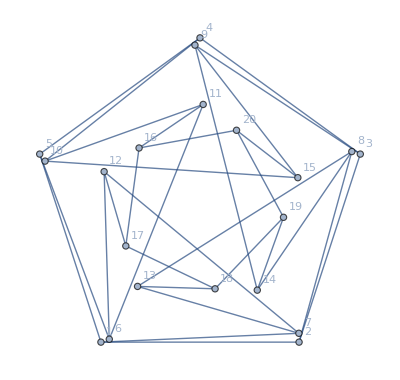

```mathematica
g=Graph[Range[20],UndirectedEdge@@@e2,VertexCoordinates->vc,VertexLabels->"Name"]
```

#### Redo

```mathematica
v=Join[
(* outer pentagon *)
Table[Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5]],{k,5}],

(* tilted pentagon *)
Table[R Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ϕ]],{k,5}],

(* middle pentagon *)
Table[1/2 r Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+ψ]],{k,5}],

(* inner pentagon *)
Table[1/2 Csc[π/5]Through[{Cos,Sin}[2π (k+1/4)/5+4π/5+θ]],{k,5}]
]/.{
ϕ->π/100,
θ->-1.70560978792577961038601596146083756671243650575033830256890571236629180161806`50.,ψ->-0.59690260418206071530790224282310554799754850595296608734085729074044126728344`50.,r->1.20786944362003084727646891808969176051871599141625694902742932477722499564001`50.,R->0.95707815686611063222867711536412461546114343529004809765978406494528295603317`50.}
```

{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0,1/(√(5/8-(√5)/8))},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{-0.91522834433436088899628632593610441365088079663511,-1.3467176124599043767205884317176684753352817356788},{0.99798344880647971716432220148780709075249481746115,-1.2865925096513834171146435780888793177907901990437},{1.5320160359066060356898895908971953053885354794036,0.55155971182432229899797521871778448701561713365772},{-0.051145467306317860688852220032846340032399338250343,1.6274751583839118693359564349540628079631245134794},{-1.5636256730724070031690732464160516424577501619793,0.45427525190305362550130035613470049814733028758538},{-0.966731579668862713970792151408505994982260897888,-0.3480447847780459359962390193223035916013944161582},{0.0322737734090878757951625399121068882306442141548,-1.026968121652366493308638700057801237972383285539},{0.9866778685808915857025223106314500736981477270835,-0.2866564197657533811983253086688129735142064653277},{0.5775266853212051019985040784228946614678184640371,0.8498047111437737329150435337502165498867539030056},{-0.6297467476423218495253967775579456284143495073874,0.8118646150523920775881594942987012532012302640195},{-0.6147438711748008540427312186896048418607775324355,0.5879598375765123816963422320207561615986538900695},{-0.74914933822783903493327575139089116873262019197331,-0.4029665827122266489831347042819774120907491167621},{0.1517441175005054133879154581088940035039606336306,-0.83700688202306423830177140624233801776305006722725},{0.84293236043600911954397822850152172490578745652751,-0.114332119195600398935571703193237342640846922264},{0.3692167314661253560441132834700802821836496342507,0.76634574635437890452413558169679661089599221618427}}

```mathematica
e=Select[Subsets[Range[20],{2}],Abs[Round[d=EuclideanDistance@@v[[#]]]-d]<=10^-2&]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-√((-1+√Times[«2»])^2+(-1/4 Plus[«2»] Power[«2»]+1/4 Power[«2»] Plus[«2»])^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-√((5/8+1/8 Power[«2»])/(5/8+Times[«2»])+(1/(√Plus[«2»])-1/4 Power[«2»] Plus[«2»])^2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{{1,2},{1,5},{1,7},{1,16},{1,17},{2,3},{2,8},{2,17},{2,18},{3,4},{3,9},{3,18},{3,19},{4,5},{4,10},{4,19},{4,20},{5,6},{5,16},{5,20},{6,11},{6,12},{7,12},{7,13},{8,13},{8,14},{9,14},{9,15},{10,11},{10,15},{11,16},{12,17},{13,18},{14,19},{15,20},{16,17},{16,20},{17,18},{18,19},{19,20}}

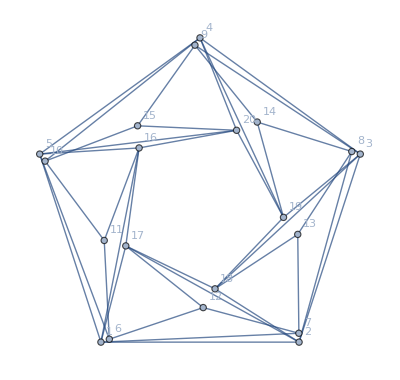

```mathematica
g0=Graph[Range[20],UndirectedEdge@@@e,VertexCoordinates->v,VertexLabels->"Name"]
```

```mathematica
RecognizeGraph[g0]
```

{}

```mathematica
VertexDegree[g0]
```

{5,5,5,5,5,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5}

```mathematica
e2=Complement[e,{{1,16},{1,17},{2,17},{2,18},{3,18},{3,19},{4,19},{4,20},{5,16},{5,20}}]
```

{{1,2},{1,5},{1,7},{2,3},{2,8},{3,4},{3,9},{4,5},{4,10},{5,6},{6,11},{6,12},{7,12},{7,13},{8,13},{8,14},{9,14},{9,15},{10,11},{10,15},{11,16},{12,17},{13,18},{14,19},{15,20},{16,17},{16,20},{17,18},{18,19},{19,20}}

```mathematica
EuclideanDistance@@v[[{4,5}]]//FullSimplify
```

2

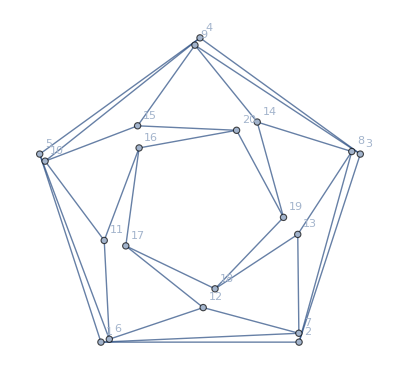

```mathematica
g=Graph[Range[20],UndirectedEdge@@@e2,VertexCoordinates->v,VertexLabels->"Name"]
```

```mathematica
r=RecognizeGraph[g]
```

DodecahedralGraph

```mathematica
GraphEdgeLengths[g]
```

{2,2,2.,2,2.,2,2.,2,2.,2.,0.999999999999999999999999999999999999999865238342,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999998652383422,0.99999999999999999999999999999999999999969546852,0.9999999999999999999999999999999999999998652383422,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999998652383422,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999996954685151,0.9999999999999999999999999999999999999998652383422,1.000000000000000000000000000000000000000018906767,1.000000000000000000000000000000000000000018906767,1.000000000000000000000000000000000000000018906767,1.000000000000000000000000000000000000000018906767,1.00000000000000000000000000000000000000001890677,1.,1.,1.,1.,1.}

```mathematica
l={{r,{0,ReplacePart[GraphData[r,"Embeddings"],10->ToCommonEdges[g,GraphData[r]]]}}}
```

{{DodecahedralGraph,{0,{{{1.548,0.503},{-1.134,-0.368},{0.,1.628},{0.957,-1.317},{-1.548,0.503},{-0.957,-1.317},{0.,2.466},{1.449,-1.995},{0.302,0.416},{0.489,-0.159},{-2.345,0.762},{-1.45,-1.995},{-0.489,-0.159},{0.7,0.965},{1.133,-0.369},{2.345,0.762},{-0.302,0.416},{0.,-0.514},{-0.7,0.965},{0.,-1.192}},{{0.,1.},{0.,-0.3},{-0.3527,0.4854},{0.5878,-0.809},{-0.2853,-0.0927},{0.,-0.6},{-0.5706,0.1854},{-0.5878,-0.809},{0.3527,0.4854},{0.5706,0.1854},{-0.5706,-0.1854},{-0.3527,-0.4854},{0.2853,-0.0927},{0.,0.6},{0.9511,0.309},{-0.9511,0.309},{0.1763,0.2427},{0.5706,-0.1854},{-0.1763,0.2427},{0.3527,-0.4854}},{{0.,1.588},{3.466,1.76},{1.002,1.086},{1.4,2.55},{2.669,1.72},{3.085,2.762},{0.948,2.186},{1.117,3.295},{1.278,0.},{1.489,0.77},{1.978,2.579},{2.187,3.348},{3.186,0.724},{0.381,0.586},{0.798,1.628},{0.281,2.623},{2.35,0.053},{2.518,1.161},{2.066,0.798},{2.464,2.262}},{{1/10 (5+√5),1/(√5)},{1/10 (-5-√5),-1/(√5)},{1/2,1/2 √(5+2 √5)},{1/2,-1/2 √(5+2 √5)},{-(2+√(2 (5+√5)))/(4 √5),1/4 (-1+1/(√5)+2 √(1+2/(√5)))},{(-2+√(2 (5+√5)))/(4 √5),1/4 (-1+1/(√5)-2 √(1+2/(√5)))},{1/4 (3+√5),√(5/8+(√5)/8)},{1/4 (3+√5),-1/2 √(1/2 (5+√5))},{1/20 (-5-3 √5-√(50-10 √5)),1/20 (-5-√5+√(10 (5+√5)))},{1/20 (-5-3 √5+√(50-10 √5)),1/20 (-5-√5-√(10 (5+√5)))},{1/20 (5+3 √5-√(50-10 √5)),1/20 (5+√5+√(10 (5+√5)))},{1/20 (5+3 √5+√(50-10 √5)),1/20 (5+√5-√(10 (5+√5)))},{1/2 (-1-√5),0},{-(-2+√(2 (5+√5)))/(4 √5),1/4 (1-1/(√5)+2 √(1+2/(√5)))},{(2+√(2 (5+√5)))/(4 √5),1/4 (1-1/(√5)-2 √(1+2/(√5)))},{1/2 (1+√5),0},{1/4 (-3-√5),√(5/8+(√5)/8)},{-1/8 (1+√5)^2,-1/2 √(1/2 (5+√5))},{-1/2,1/2 √(5+2 √5)},{-1/2,-1/2 √(5+2 √5)}},{{0.5,0.866},{-0.5,-0.866},{0.5,-0.866},{-0.618,1.902},{-0.618,-1.902},{-1.,0.},{-0.354,-0.354},{-1.618,1.176},{2.,0.},{1.618,1.176},{-1.618,-1.176},{-2.,0.},{0.354,-0.354},{1.,0.},{0.618,1.902},{-0.354,0.354},{1.618,-1.176},{0.354,0.354},{0.618,-1.902},{-0.5,0.866}},{{0.951,0.309},{-0.951,-0.309},{0.588,0.809},{0.809,-0.588},{-0.809,-0.588},{-0.588,0.809},{0.309,0.951},{0.951,-0.309},{0.,-1.},{0.309,-0.951},{0.,1.},{-0.309,0.951},{-1.,0.},{0.809,0.588},{0.588,-0.809},{1.,0.},{-0.309,-0.951},{-0.951,0.309},{-0.588,-0.809},{-0.809,0.588}},{{0.,1.034},{3.249,1.921},{1.626,0.},{0.535,2.867},{3.25,1.036},{2.712,2.868},{1.625,1.056},{1.091,2.659},{1.092,0.296},{0.724,1.249},{2.526,1.706},{2.156,2.66},{2.526,1.251},{0.537,0.087},{0.,1.919},{0.723,1.705},{2.159,0.297},{1.624,1.9},{2.714,0.088},{1.623,2.957}},{{-0.1928,-0.1065},{-2.6314,0.},{0.4662,-0.4662},{-1.309,0.5},{3.0583,-3.0583},{2.6314,0.},{0.,-0.8999},{-1.309,-0.5},{0.4662,0.4662},{0.,0.8999},{0.,-2.3999},{-3.0583,-3.0583},{3.0583,3.0583},{0.2461,0.1065},{-0.4662,0.4662},{-0.4662,-0.4662},{1.309,0.5},{0.,2.3999},{1.309,-0.5},{-3.0583,3.0583}},{{0,3},{4,2},{1,3},{5,0},{2,2},{4,1},{1,1},{3,0},{3,4},{5,4},{2,1},{3,1},{4,3},{1,4},{6,1},{1,0},{3,3},{5,3},{2,3},{5,1}},{{-1,(-1-√5)/(4 √(5/8-(√5)/8))},{0.3692167314661253560441132834700802821836496342507,0.76634574635437890452413558169679661089599221618427},{√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0.0322737734090878757951625399121068882306442141548,-1.026968121652366493308638700057801237972383285539},{-0.6297467476423218495253967775579456284143495073874,0.8118646150523920775881594942987012532012302640195},{-0.6147438711748008540427312186896048418607775324355,0.5879598375765123816963422320207561615986538900695},{0,1/(√(5/8-(√5)/8))},{-0.91522834433436088899628632593610441365088079663511,-1.3467176124599043767205884317176684753352817356788},{1.5320160359066060356898895908971953053885354794036,0.55155971182432229899797521871778448701561713365772},{0.9866778685808915857025223106314500736981477270835,-0.2866564197657533811983253086688129735142064653277},{-1.5636256730724070031690732464160516424577501619793,0.45427525190305362550130035613470049814733028758538},{-0.966731579668862713970792151408505994982260897888,-0.3480447847780459359962390193223035916013944161582},{0.84293236043600911954397822850152172490578745652751,-0.114332119195600398935571703193237342640846922264},{1,(-1-√5)/(4 √(5/8-(√5)/8))},{0.99798344880647971716432220148780709075249481746115,-1.2865925096513834171146435780888793177907901990437},{-√((5/8+(√5)/8)/(5/8-(√5)/8)),(-1+√5)/(4 √(5/8-(√5)/8))},{0.5775266853212051019985040784228946614678184640371,0.8498047111437737329150435337502165498867539030056},{0.1517441175005054133879154581088940035039606336306,-0.83700688202306423830177140624233801776305006722725},{-0.051145467306317860688852220032846340032399338250343,1.6274751583839118693359564349540628079631245134794},{-0.74914933822783903493327575139089116873262019197331,-0.4029665827122266489831347042819774120907491167621}},{{1/4 (-1+√5),-1/2 √(1/2 (5+√5))},{1/4 (1-√5),√(5/8+(√5)/8)},{1,0},{1/4 (-1-√5),-1/2 √(1/2 (5-√5))},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{2,0},{1/2 (-1-√5),-√(1/2 (5-√5))},{1/2 (1+√5),-√(1/2 (5-√5))},{1/2 (1-√5),-√(1/2 (5+√5))},{1/2 (-1+√5),√(1/2 (5+√5))},{1/2 (-1-√5),√(1/2 (5-√5))},{1/2 (1-√5),√(1/2 (5+√5))},{1/4 (1+√5),-1/2 √(1/2 (5-√5))},{1/4 (1-√5),-1/2 √(1/2 (5+√5))},{1/2 (-1+√5),-√(1/2 (5+√5))},{1/2 (1+√5),√(1/2 (5-√5))},{-2,0},{1/4 (1+√5),√(5/8-(√5)/8)},{-1,0}},{{1/4 (-1+√5),-1/2 √(1/2 (5+√5))},{1/4 (1-√5),√(5/8+(√5)/8)},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-1/2 √(1/2 (5-√5))},{1,0},{1/2 (-1+√5),√(1/2 (5+√5))},{1/2 (-1-√5),√(1/2 (5-√5))},{-2,0},{1/2 (1+√5),√(1/2 (5-√5))},{1/2 (-1-√5),-√(1/2 (5-√5))},{2,0},{1/2 (1-√5),√(1/2 (5+√5))},{-1,0},{1/4 (1+√5),√(5/8-(√5)/8)},{1/2 (-1+√5),-√(1/2 (5+√5))},{1/2 (1+√5),-√(1/2 (5-√5))},{1/2 (1-√5),-√(1/2 (5+√5))},{1/4 (1+√5),-1/2 √(1/2 (5-√5))},{1/4 (1-√5),-1/2 √(1/2 (5+√5))}},{{1/4 (-1+√5),-1/2 √(1/2 (5+√5))},{1/4 (1-√5),√(5/8+(√5)/8)},{1,0},{-2,0},{1/2 (1-√5),√(1/2 (5+√5))},{1/4 (1+√5),-1/2 √(1/2 (5-√5))},{1/4 (-1-√5),-1/2 √(1/2 (5-√5))},{1/2 (-1+√5),√(1/2 (5+√5))},{1/2 (-1-√5),√(1/2 (5-√5))},{1/2 (1+√5),√(1/2 (5-√5))},{1/2 (-1-√5),-√(1/2 (5-√5))},{1/2 (1+√5),-√(1/2 (5-√5))},{1/4 (1-√5),-1/2 √(1/2 (5+√5))},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/2 (-1+√5),-√(1/2 (5+√5))},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/2 (1-√5),-√(1/2 (5+√5))},{1/4 (1+√5),√(5/8-(√5)/8)},{2,0},{-1,0}},{{2/(1+√5),0},{-2/(1+√5),0},{-1/2,1/2 √(5-2 √5)},{-1/2,-1/2 √(5-2 √5)},{1/4 (3-√5),-1/2 √(1/2 (5-√5))},{1/4 (3-√5),1/2 √(1/2 (5-√5))},{1/2 (1/(√5)-√(1/2 (1-1/(√5)))),1/4 (-1-1/(√5)-2 √(1-2/(√5)))},{(2+√(10-2 √5))/(4 √5),1/4 (-1-1/(√5)+2 √(1-2/(√5)))},{1/20 (-5+3 √5+√(10 (5+√5))),1/20 (-5+√5+√(50-10 √5))},{1/20 (-5+3 √5-√(10 (5+√5))),1/20 (-5+√5-√(50-10 √5))},{1/20 (5-3 √5+√(10 (5+√5))),1/20 (5-√5+√(50-10 √5))},{1/20 (5-3 √5-√(10 (5+√5))),1/20 (5-√5-√(50-10 √5))},{1/10 (5-√5),-1/(√5)},{1/4 (-3+√5),-1/2 √(1/2 (5-√5))},{1/4 (-3+√5),1/2 √(1/2 (5-√5))},{1/10 (-5+√5),1/(√5)},{-(2+√(10-2 √5))/(4 √5),1/4 (1+1/(√5)-2 √(1-2/(√5)))},{(-2+√(10-2 √5))/(4 √5),1/4 (1+1/(√5)+2 √(1-2/(√5)))},{1/2,1/2 √(5-2 √5)},{1/2,-1/2 √(5-2 √5)}}}}}}

```mathematica
PropertyReplace[l,"Embeddings","12.1"]
```

12.1/GraphData34.m...

{{GraphData34-2.m}}

```mathematica
RenameGraphFiles[]
```

{}

{}

{}

«5 more identical outputs»

{12.1/GraphData34-2.m}

{{},{},{},{},{},{},{},{},{/Users/eww/Documents/Mathematica/Paclets/GraphData/Paclet/12.1/GraphData34.m}}

### UnitDistance

```mathematica
r=FullSimplify[Sin[(n+1-2k)/(2(n+1))π]/Sin[(2k)/(n+1)π]/.{n->9,k->2}];
R=FullSimplify[Sin[(n+1-2k)/(2(n+1))π]/Sin[(2k)/(n+1)π]/.{n->9,k->1}];
```

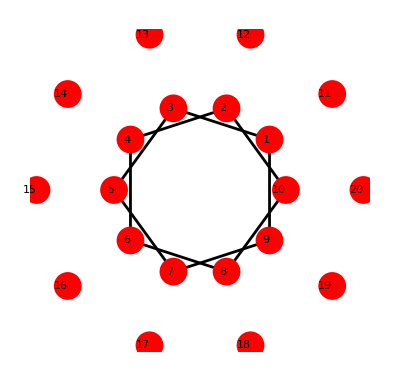

```mathematica
ShowLabeledGraph[g=Graph[List/@Join[
Partition[Range[1,9,2],2,1,1],
Partition[Range[2,10,2],2,1,1]
],List/@Join[
Table[r Through[{Cos,Sin}[(2π i)/10]],{i,10}],
Table[R Through[{Cos,Sin}[(2π i)/10]],{i,10}]
]]]
```

```mathematica
Norm[Subtract@@v[[{1,3}]]]//FullSimplify
```

1

```mathematica
Norm[Subtract@@v[[{12,13}]]]//FullSimplify
```

1

Rehashing named triangle objects...

```mathematica
v=Combinatorica`Vertices[g];
```

```mathematica
p=Intersections[Circle[{0,0},R],Line[v[[{3,5}]]]][[1,1]]//FullSimplify
```

{1/8 (√(34+6 √5)+Root[16-100 #1^2+5 #1^4&,1]),(√5+√(25+8 √5))/(10-2 √5)}

```mathematica
p//N
```

{0.303986,1.58922}

```mathematica
Solve[Norm[R{Cos[a],Sin[a]}-v[[3]]]==1,a]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→ArcSec[Root[80+160 #1+100 #1^2+20 #1^3+#1^4&,3]]},{a→ArcSec[Root[80-160 #1+100 #1^2-20 #1^3+#1^4&,3]]}}

```mathematica
N[%]
```

{{a→2.43853},{a→1.33138}}

```mathematica
ang=3(2π/10)-ArcSec[Root[80-160 #1+100 #1^2-20 #1^3+#1^4&,3]];
```

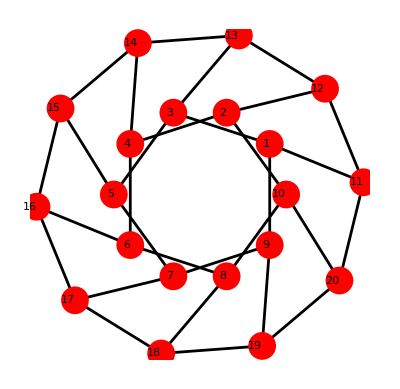

```mathematica
ShowLabeledGraph[g=Graph[List/@Join[
Partition[Range[1,9,2],2,1,1],
Partition[Range[2,10,2],2,1,1],
{#,#+10}&/@Range[10],
Partition[Range[11,20],2,1,1]
],List/@Join[
Table[r Through[{Cos,Sin}[(2π i)/10]],{i,10}],
Table[R Through[{Cos,Sin}[(2π i)/10-ang]],{i,10}]
]]]
```

```mathematica
v=Combinatorica`Vertices[g];
Norm[Subtract@@v[[{3,13}]]]//FullSimplify
```

1

```mathematica
RecognizeGraph[g]
```

Getting index for CanonicalForm (first time only)...

DodecahedralGraph

```mathematica
tilt=ArcTan@@Subtract@@v[[{19,18}]]//FullSimplify
```

ArcTan[Root[-1+8 #1+66 #1^2+72 #1^3+19 #1^4&,4]]

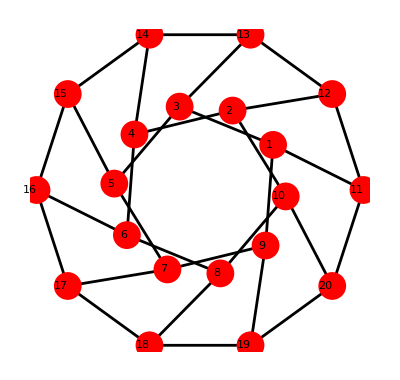

```mathematica
ShowLabeledGraph[g=Graph[List/@Join[
Partition[Range[1,9,2],2,1,1],
Partition[Range[2,10,2],2,1,1],
{#,#+10}&/@Range[10],
Partition[Range[11,20],2,1,1]
],List/@Join[
Table[r Through[{Cos,Sin}[(2π i)/10-tilt]],{i,10}],
Table[R Through[{Cos,Sin}[(2π i)/10-ang-tilt]],{i,10}]
]]]
```

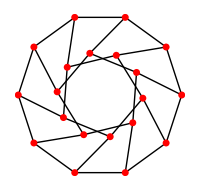

```mathematica
GraphPlot[g,Method->None,ImageSize->200]
```

```mathematica
v=Combinatorica`Vertices[g]//FullSimplify//ToRadicals
```

{{1/10 (5+√5),1/(√5)},{1/4+3/(4 √5)-1/2 √(1/2 (1-1/(√5))),1/4+1/(4 √5)+1/2 √(1/2+1/(2 √5))},{1/(2 √5)-1/2 √(1/2+1/(2 √5)),1/4 (1-1/(√5)+2 √(1+2/(√5)))},{1/2 (-1/(√5)-√(1/2+1/(2 √5))),-1/4+1/(4 √5)+1/2 √(1+2/(√5))},{1/4 (-1-3/(√5)-√(2 (1-1/(√5)))),1/4 (-1-1/(√5)+2 √(1/2+1/(2 √5)))},{1/10 (-5-√5),-1/(√5)},{1/4 (-1-3/(√5)+√(2 (1-1/(√5)))),1/4 (-1-1/(√5)-2 √(1/2+1/(2 √5)))},{1/2 (-1/(√5)+√(1/2+1/(2 √5))),-1/4+1/(4 √5)-1/2 √(1+2/(√5))},{1/(2 √5)+1/2 √(1/2+1/(2 √5)),1/4 (1-1/(√5)-2 √(1+2/(√5)))},{1/4+3/(4 √5)+1/2 √(1/2 (1-1/(√5))),1/4+1/(4 √5)-1/2 √(1/2+1/(2 √5))},{1/2 (1+√5),0},{1/4 (3+√5),√(5/8+(√5)/8)},{1/2,√(5/4+(√5)/2)},{-1/2,√(5/4+(√5)/2)},{1/4 (-3-√5),√(5/8+(√5)/8)},{1/2 (-1-√5),0},{-1/8 (1+√5)^2,-√(5/8+(√5)/8)},{-1/2,-√(5/4+(√5)/2)},{1/2,-√(5/4+(√5)/2)},{1/4 (3+√5),-√(5/8+(√5)/8)}}

```mathematica
<<Utilities`Simplify`
```

General::obspkg: NumberTheory`Recognize` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
SymbolicUnion[Norm/@Subtract@@@(Edges[g]/.Thread[Range[20]->v])]//FullSimplify
```

{1}

```mathematica
Insert[GraphData["DodecahedralGraph","Embeddings"],ToCommonEdges[ChangeVertices[g,v],"DodecahedralGraph"],4]
```

{{{1.548,0.503},{-1.134,-0.368},{0.,1.628},{0.957,-1.317},{-1.548,0.503},{-0.957,-1.317},{0.,2.466},{1.449,-1.995},{0.302,0.416},{0.489,-0.159},{-2.345,0.762},{-1.45,-1.995},{-0.489,-0.159},{0.7,0.965},{1.133,-0.369},{2.345,0.762},{-0.302,0.416},{0.,-0.514},{-0.7,0.965},{0.,-1.192}},{{0.,1.},{0.,-0.3},{-0.3527,0.4854},{0.5878,-0.809},{-0.2853,-0.0927},{0.,-0.6},{-0.5706,0.1854},{-0.5878,-0.809},{0.3527,0.4854},{0.5706,0.1854},{-0.5706,-0.1854},{-0.3527,-0.4854},{0.2853,-0.0927},{0.,0.6},{0.9511,0.309},{-0.9511,0.309},{0.1763,0.2427},{0.5706,-0.1854},{-0.1763,0.2427},{0.3527,-0.4854}},{{0.,1.588},{3.466,1.76},{1.002,1.086},{1.4,2.55},{2.669,1.72},{3.085,2.762},{0.948,2.186},{1.117,3.295},{1.278,0.},{1.489,0.77},{1.978,2.579},{2.187,3.348},{3.186,0.724},{0.381,0.586},{0.798,1.628},{0.281,2.623},{2.35,0.053},{2.518,1.161},{2.066,0.798},{2.464,2.262}},{{1/10 (5+√5),1/(√5)},{1/10 (-5-√5),-1/(√5)},{1/2,√(5/4+(√5)/2)},{1/2,-√(5/4+(√5)/2)},{1/2 (-1/(√5)-√(1/2+1/(2 √5))),-1/4+1/(4 √5)+1/2 √(1+2/(√5))},{1/2 (-1/(√5)+√(1/2+1/(2 √5))),-1/4+1/(4 √5)-1/2 √(1+2/(√5))},{1/4 (3+√5),√(5/8+(√5)/8)},{1/4 (3+√5),-√(5/8+(√5)/8)},{1/4 (-1-3/(√5)-√(2 (1-1/(√5)))),1/4 (-1-1/(√5)+2 √(1/2+1/(2 √5)))},{1/4 (-1-3/(√5)+√(2 (1-1/(√5)))),1/4 (-1-1/(√5)-2 √(1/2+1/(2 √5)))},{1/4+3/(4 √5)-1/2 √(1/2 (1-1/(√5))),1/4+1/(4 √5)+1/2 √(1/2+1/(2 √5))},{1/4+3/(4 √5)+1/2 √(1/2 (1-1/(√5))),1/4+1/(4 √5)-1/2 √(1/2+1/(2 √5))},{1/2 (-1-√5),0},{1/(2 √5)-1/2 √(1/2+1/(2 √5)),1/4 (1-1/(√5)+2 √(1+2/(√5)))},{1/(2 √5)+1/2 √(1/2+1/(2 √5)),1/4 (1-1/(√5)-2 √(1+2/(√5)))},{1/2 (1+√5),0},{1/4 (-3-√5),√(5/8+(√5)/8)},{-1/8 (1+√5)^2,-√(5/8+(√5)/8)},{-1/2,√(5/4+(√5)/2)},{-1/2,-√(5/4+(√5)/2)}},{{0.5,0.866},{-0.5,-0.866},{0.5,-0.866},{-0.618,1.902},{-0.618,-1.902},{-1.,0.},{-0.354,-0.354},{-1.618,1.176},{2.,0.},{1.618,1.176},{-1.618,-1.176},{-2.,0.},{0.354,-0.354},{1.,0.},{0.618,1.902},{-0.354,0.354},{1.618,-1.176},{0.354,0.354},{0.618,-1.902},{-0.5,0.866}},{{0.951,0.309},{-0.951,-0.309},{0.588,0.809},{0.809,-0.588},{-0.809,-0.588},{-0.588,0.809},{0.309,0.951},{0.951,-0.309},{0.,-1.},{0.309,-0.951},{0.,1.},{-0.309,0.951},{-1.,0.},{0.809,0.588},{0.588,-0.809},{1.,0.},{-0.309,-0.951},{-0.951,0.309},{-0.588,-0.809},{-0.809,0.588}},{{0.,1.034},{3.249,1.921},{1.626,0.},{0.535,2.867},{3.25,1.036},{2.712,2.868},{1.625,1.056},{1.091,2.659},{1.092,0.296},{0.724,1.249},{2.526,1.706},{2.156,2.66},{2.526,1.251},{0.537,0.087},{0.,1.919},{0.723,1.705},{2.159,0.297},{1.624,1.9},{2.714,0.088},{1.623,2.957}},{{-0.1928,-0.1065},{-2.6314,0.},{0.4662,-0.4662},{-1.309,0.5},{3.0583,-3.0583},{2.6314,0.},{0.,-0.8999},{-1.309,-0.5},{0.4662,0.4662},{0.,0.8999},{0.,-2.3999},{-3.0583,-3.0583},{3.0583,3.0583},{0.2461,0.1065},{-0.4662,0.4662},{-0.4662,-0.4662},{1.309,0.5},{0.,2.3999},{1.309,-0.5},{-3.0583,3.0583}},{{0,3},{4,2},{1,3},{5,0},{2,2},{4,1},{1,1},{3,0},{3,4},{5,4},{2,1},{3,1},{4,3},{1,4},{6,1},{1,0},{3,3},{5,3},{2,3},{5,1}}}

## GraphData

### GraphClassString

```mathematica
GraphClassString["DodecahedralGraph"]
```

\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Biconnected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Bridgeless Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Class 1 Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Completely Regular Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Connected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Cubic Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Cyclic Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Determined by Spectrum Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Distance-Regular Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Edge-Transitive Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Generalized Petersen Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Hamiltonian Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:LCF Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Noneulerian Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Planar Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Platonic Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Polyhedral Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Regular Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Square-Free Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Symmetric Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Traceable Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Triangle-Free Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Unitransitive Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Vertex-Transitive Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Weakly Regular Graphs}